# Supporting Information for Massively Increasing the number of Antibody-Virus Interactions across Studies

The following code reproduces the plots in the main text. Made on Mathematica version 13.2.0 for Windows. Sections can be opened by mouse click.

Raw data can be found here.

## Figures

### Accessing the Data

In this work, we analyze seven large influenza datasets measuring serum-virus inhibition. Values represent hemagglutination inhibition (HAI) titers, with larger values representing stronger antibody inhibition. We refer to these datasets in the code as follows:

table="S1": Fonville Table S1, called Dataset_Ferret in our paper

table="S3": Fonville Table S3, called Dataset_(Infect,1) in our paper

table="S5": Fonville Table S5, called Dataset_(Vac,1) in our paper

table="S6": Fonville Table S6, called Dataset_(Vac,2) in our paper

table="S13": Fonville Table S13, called Dataset_(Vac,3) in our paper

table="S14": Fonville Table S14, called Dataset_(Vac,4) in our paper

table="Vinh": Vinh Dataset, called Dataset_(Infect,2) in our paper

#### Fonville 2014

For each dataset, the variables viruses and sera contain all the viruses and sera in that study. For example, here are the viruses and sera in Table S1

```mathematica
viruses["S1"]//Short
sera["S1"]//Short
```

{NL/179/93,A/WELLINGTON/1/94,A/BRISBANE/22/94,«68»,VN020/EL443/2010,VN021/EL444/2010,VN053/2010}

{Serum_A/WELLINGTON/25/93_TableS1,Serum_A/WELLINGTON/96/93_TableS1,«32»,Serum_A/HONGKONG/34/90_TableS1}

The sera are all labeled with their associated table for easy reference. Sera from Tables S5, S6, S13, and S14 [the vaccination studies] also have “_Pre” or “_Post” appended to their names to denote whether they were drawn pre- or post-vaccination. Below is one example from each Fonville study

```mathematica
First/@sera/@fonvilleTables//Column
```

Serum_A/WELLINGTON/25/93_TableS1
Subject1Year2007_TableS3
Subject258Age29_TableS5_Pre
Subject71Age18_TableS6_Pre
SubjectA028_TableS13_Pre
SubjectB007_TableS14_Pre

For convenience, the table index All can be used to get a list of the viruses or sera in all Fonville studies

```mathematica
viruses[All]//Short
sera[All]//Short
```

{A/AUCKLAND/20/2003,A/AUCKLAND/5/96,A/BANGKOK/1/97,«75»,VN020/EL443/2010,VN021/EL444/2010,VN053/2010}

{Serum_A/WELLINGTON/25/93_TableS1,Serum_A/WELLINGTON/96/93_TableS1,«1144»,SubjectB039_TableS14_Post}

Measurements are accessed via the data master function. As shown below, every virus-serum pair from the same table will either have a measurement or will be Missing[]. If a virus was not included in a table, then its interaction with a serum will not evaluate. Below are examples of each type of evaluation

```mathematica
data[{viruses["S1"][[1]],sera["S1"][[1]]}]
data[{viruses["S1"][[-1]],sera["S1"][[1]]}]
data[{viruses["S3"][[1]],sera["S1"][[1]]}]
```

640.

Missing[]

data[{BI/16190/68,Serum_A/WELLINGTON/25/93_TableS1}]

The code below displays all measurements from Table S1 as an ArrayPlot, with missing measurements shown in dark-red

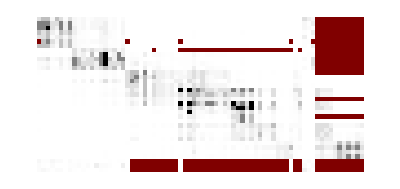

```mathematica
(* Raw data *)
ArrayPlot@Table[data[{virus,serum}],{serum,sera["S1"]},{virus,viruses["S1"]}]
```

The following grid shows the number of sera and viruses in each Fonville Study

```mathematica
showGrid[Prepend[{#,Length@sera[#],Length@viruses[#]}&/@fonvilleTables,{"Study","# of Sera","# of Viruses"}]]
```

Study | # of Sera | # of Viruses
S1 | 35 | 74
S3 | 324 | 57
S5 | 212 | 70
S6 | 256 | 70
S13 | 160 | 20
S14 | 160 | 20

#### Vinh 2021

The Vinh dataset can be accessed just like the Fonville datasets using the data master function

```mathematica
data[{viruses["Vinh"][[1]],sera["Vinh"][[1]]}]
```

1810.

Below is the number of viruses and sera in the long-and-skinny Vinh dataset

The full Vinh dataset contains 24,400 (10x more) sera than what is shown below. In this notebook, we only load every 10th Vinh serum to speed up initialization. The full Vinh serum can be loaded in the Initialization section

```mathematica
Echo[Length@viruses["Vinh"],"# of Viruses in Vinh"];
Echo[Length@sera["Vinh"],"# of Sera in Vinh"];
```

# of Viruses in Vinh  6

# of Sera in Vinh  2440

### An Anecdote showing the Power of Matrix Completion

In this manuscript, we develop a new form of matrix completion that predicts the values±error for a virus-of-interest in a table-of-interest. As described in Figure 1 of our manuscript, the main steps in the algorithm are:

Step 1: Train decision trees that can predict the values of the virus-of-interest in other datasets using values from other viruses

Step 2: Use the values from these other viruses to predict the values of the virus-of-interest in the dataset-of-interest

Step 3: Use other decision trees (predicting other viruses in the table-of-interest) to quantify the transferability between the datasets. With this transferability, quantify the uncertainty of the predictions for the virus-of-interest

Below, we walk through these steps and predict the behavior of the following virus:

```mathematica
{virusOfInterest,tableOfInterest}={"A/PERTH/16/2009","S6"};
```

Step 1: Training decision trees
In this notebook, we have already pre-trained decision trees to predict this (and all other) virus-dataset pairs. The results are stored in the master functions leaveOneOutFonville and leaveOneOutVinh, used to predict viruses in the Fonville and Vinh datasets, respectively [see the Initialization for details on how to grow these decision trees].

Here is an example of a decision tree predicting this virus from Table S1→S6. Each tree has the form {tablePredictingFrom,virusFeatures,trainingError,actualError,decisionTree}

```mathematica
leaveOneOutFonville[{virusOfInterest,tableOfInterest}][[4]]
```

{S1,{A/VICTORIA/361/2011,A/WELLINGTON/1/2004,A/BRISBANE/3/2005,A/SYDNEY/5/97,A/SYDNEY/5/97},0.561163,0.780025,PredictorFunction[…]}

The first element shows that this decision tree was trained in Fonville Table S1 to predict the values of virusOfInterest="A/PERTH/16/2009" using data from {"A/VICTORIA/361/2011","A/WELLINGTON/1/2004","A/BRISBANE/3/2005","A/SYDNEY/5/97","A/SYDNEY/5/97"}

In other words, if we know the HAI titers of these five viruses for any serum, then we can predict the values of "A/PERTH/16/2009" for this same serum using this decision tree

This tree has an RMSE of 0.561 in Table S1 on the 70% of sera that were not used for training. It also had an RMSE of 0.780 when applied in Table S6. Note that this latter RMSE is somewhat larger, as will often be the case when extrapolating virus behavior across datasets

RMSE is calculated using Log_10[HAI Titers]. Thus, an RMSE of 0.561 corresponds to 10^0.561=3.6-fold error

The final entry in each list stores the decisionTree (as a PredictorFunction) for further calculations

Below is another decision tree predicting this virus from Table S14→S6. This decision tree uses a different set of viruses (features) and was also trained in a different dataset, and both its training RMSE of 0.404 and its actual RMSE 0.455 are slightly lower than what we saw above

```mathematica
tree=leaveOneOutFonville[{virusOfInterest,tableOfInterest}][[-4]]
```

{S14,{A/VICTORIA/1/93,NL/620/89,BI/16190/68,A/CHRISTCHURCH/1/96,A/NEW_YORK/55/2004},0.403828,0.455036,PredictorFunction[…]}

Step 2: Predicting values for the virus-of-interest
Predicting values using a decision tree is easy...the difficult part (i.e. the secret sauce in this recipe) will be to compute the uncertainty of these predictions! The following code uses the second tree from above to predict values for the virus-of-interest

It is critically important for decision trees to work on row centered data (which adds numerical stability and lets us make accurate inferences across very diverse datasets). We use the rowCenteredData function to get these centered data, noting that we do not include values for the virus-of-interest when row centering (which would be cheating)

The decision tree is then applied to this row-centered data subsetTesting, which is then un-centered using shiftTesting. The ReplacePart ensures that we only consider predictions whenever values are available for all five viruses used by the decision tree - if any values are missing, then the prediction is given as Missing[]

```mathematica
{subsetTesting,shiftTesting}=rowCenteredData[tree[[2]],tableOfInterest];
ReplacePart[tree[[-1]][subsetTesting]+shiftTesting,Position[subsetTesting,_Missing,{2},Heads->False][[All,{1}]]->Missing[]]
```

Step 3: Estimating the uncertainty of the predictions
Now comes the tricky part, which has rarely been investigated: How can we determine the confidence in these predictions without using accessing the measurements for the virus of interest?

Our solution was to make additional predictions for many other viruses from Table S14→S6. Since we have access to their values in both datasets, we can directly compare our predictions with the measurements. The plot below shows the results of doing this many times for many different viruses

The x-axis (σ_Training) shows the RMSE of the decision tree on its training set in Table S14, while the y-axis (σ_Actual) shows the RMSE of the predictions in Table S6. Both of these values are stored in the 3rd and 4th elements of each decision tree, which is why this plot can be computed so quickly

For leave-one-out or leave-multi-out analysis, it is very important to not use any withheld data. In this case, it means that whenever we use decisions trees to predict other viruses between Table S14→S6, none of those decision trees should use virusOfInterest="A/PERTH/16/2009" as one of their features! In the code below, the second argument in compareTables[...,{virusOfInterest},...] defines the virus whose values should not be held. More generally, in every part of our algorithm we were careful to propagate these withheld viruses across all functions so that they were never accessed

The data below represents the top 10 decision trees when predicting any other virus from Table S14→S6, since we only want to use the best decision trees when making our predictions. Moreover, we are most interested in defining the “top-left border” of this cluster of points, which will tell us how to use σ_Training to estimate an upper bound on σ_Actual. More details are given in the Initialization section

The transferability y=0.186+1.105x has a nearly-diagonal slope, indicating a strong transferability. In other words, a decision tree with low (or high) training error σ_Training will have a correspondingly low (or high) actual error σ_Actual

For other datasets with steeper transferability functions such as S5→S1 (Vac 1→Ferret in Figure S1), low training error may still translate to low actual error, but a slight increase in training error can result in very large actual error, representing a high uncertainty in the predictions

For the decision tree above for our virus-of-interest, which has a training RMSE of σ_Training=0.404, we would use the transferability to estimate the uncertainty of its predictions as σ_Predict=0.186+1.105 σ_Training=0.632 (or equivalently 10^0.632=4.3-fold error)

```mathematica
Grid[{{Show[compareTables["S14"->"S6",{virusOfInterest},"ShowPlot"->True],PlotLabel->font["S14→S6",14],FrameLabel->font/@{"σ_Training","σ_Actual"},FrameTicks->Automatic,ImageSize->130],Labeled[font@compareTables["S14"->"S6",{virusOfInterest}]/.val_Real:>Round[val,0.001],font["Transferability",Bold],Top]}}]
```

-Graphics- | 0.186+1.105 xTransferability

At this point, we have all the pieces to predict the values±error for the virus-of-interest in the table-of-interest from Table S14→S6. First, we will find the top 5 decision trees (with the lowest σ_Training) and use each of them to predict the values of "A/PERTH/16/2009" in Table S6. We average their five predictions (ignoring any Missing[] predictions) to ameliorate overfitting

We then compute σ_Predict for each of these top 5 trees, averaging over these 5 values to estimate the uncertainty of our predictions (in Log_10 units). Finally, after making these predictions, we can compare against experimental measurements to see how we did. The following code carries out these predictions and then plots them as a swarm plot (because the HAI titers have discrete values)

HAI measurements of 5 are all shown in blue, measurements of 10 are shown in gold... Values cluster around the diagonal , signifying that the predictions are highly accurate (although in this case most of the predictions were concentrated at very low values which are likely easy to predict)

Error is shown in two ways: First, each prediction has an error bar representing its uncertainty. Second the diagonal bands represent σ_Predict, so that with Gaussian-distributed noise around 68% of the data should fall within this gray band. σ_Predict and σ_Actual are shown in the top-left of the plot, demonstrating that we have heavily overestimated the error

The histogram on the right shows the distribution of measurements (M) that are within 0.5, 1.0, 1.5... standard deviations (σ) of the predictions (μ). For Gaussian-distributed noise, this distribution should follow the black dashed line. From this vantage, we once again find that we have overestimated the error. We note, however, that our algorithm was purposefully designed to overestimate rather than underestimate error. That way, although we may occasionally have tight predictions that we claim are highly uncertain, we avoid having poor predictions that we claim are accurate

The option "OtherTables"->{"S14"} specifies that these predictions should solely be based using decision trees from Table S14→S6

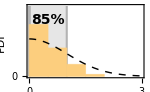
{-Graphics-,-Graphics-}

```mathematica
plotCompletion[completionPredictions[{virusOfInterest,tableOfInterest},"OtherTables"->{"S14"}],"PlotType"->"Swarm"]
```

Now here is a riddle for you, dear reader: How do we know what dataset would yield the most accurate predictions?
(Mouse-click to expand this section and find out!)

The answer is...that we have no idea. A priori, it is hard to tell which table has similar virus patterns to Table S6. In fact, if we were in “the wild,” without access to measurements from the virus-of-interest, all we would know is that our predictions have 4.4-fold uncertainty, and we may want to decrease this error further

Fortunately, all we need to do is add more datasets - it doesn’t matter which ones, simply add them all! Any datasets that are unrelated to Table S6 will have a large σ_Predict and will negligibly contribute to the predictions, whereas those with small σ_Predict will contribute a lot. In this case, let’s see how accurately the other datasets would predict the virus-of-interest. (Remember that this is technically peeking behind the curtain, since we don’t have access to data from the virus-of-interest, but we can let σ_Predict guide our confidence in each set of predictions)

Tables S1 and S3 have massive σ_Predict and should be ignored (even though both of their σ_Actual turn out to be quite small). The reason for this discrepancy is that Table S1/S3 and Table S6 have very different virus-serum inhibition patterns in their datasets. Some viruses will be very accurately predicted while others will not, but σ_Training is unable to always differentiate between the two cases. In our lingo, this means that there is small transferability between S1→S6 and between S3→S6. Said another way, although these predictions were accurate for this virus-of-interest, many other viruses will be very poorly predicted between these tables

Tables S13 and S14 have smaller σ_Predict values, but Table S5 has the smallest estimated error. And, indeed, we find that σ_Actual is smallest for Table S5. Hence, when these predictions are all combined together, the main contribution will be from Table S5

```mathematica
Grid[plotCompletion[completionPredictions[{virusOfInterest,tableOfInterest},"OtherTables"->{#}],"PlotType"->"Swarm",PlotLabel->font[#->tableOfInterest,14]]&/@DeleteCases[fonvilleTables,tableOfInterest]]
```

-Graphics-

The default behavior for our code is to utilize all datasets to predict a virus's behavior. In this case, when consider all datasets, we infer essentially the same results as when using just the Table S5→S6 prediction. Importantly, the algorithm figured this out itself, deriving all relationships between these tables in a data-driven manner!

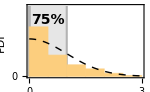
{-Graphics-,-Graphics-}

```mathematica
plotCompletion[completionPredictions[{virusOfInterest,tableOfInterest}],"PlotType"->"Swarm"]
```

To summarize, if we want to predict the virus-of-interest, we may start off by trying to predict it using one dataset (Fonville Table S14→S6) and find an unacceptably large σ_Predict=4.3-fold. At this point, we need to start hunting for additional datasets, and we can safely throw them all into the pot, knowing that the unimportant ones will not hurt us while the important ones will bring down σ_Predict (and with it σ_Actual). In this case, after including all of our datasets, we end up with a comfortable σ_Predict=1.9-fold (comparable to the noise of the HAI assay), and indeed, upon peeking behind the curtain we find that these predictions are σ_Actual=1.8-fold accurate.

#### A Final Note about the Random Forests in this Notebook

An important point about the random forests leaveOneOutFonville and leaveOneOutVinh in this notebook is that they are trimmed down versions of the full forests we used in our manuscript. This has several important implications:

Larger forests lead to better prediction accuracy (lower σ_Predict and σ_Actual), because they explore more relationships between the viruses

The full forest for leave-one-out analysis used in our manuscript had ~45,000 decision trees, whereas the forests in this notebook contain 5,650 trees. We trimmed the forests because they reduced the size of the notebook by 10x, but as a result the figures below will not perfectly reproduce the figures in our manuscript, but instead provide worse predictions. We apologize for this lack of direct reproducibility, but we hope that the increased initialization speed of this notebook is worth the tradeoff

```mathematica
(* Number of decision trees in the leave-one-out forests in this notebook *)
Total[Length/@leaveOneOutFonville]+Total[Length/@leaveOneOutVinh]
```

5232

The full random forests used in our work can be recovered from this notebook, as described in the Initialization section. We recommend that anyone going down this route should export their resulting forests in a Compressed file that can then be Imported in following sessions

In addition to the leave-one-out forests, we also grew additional forests specifically suited for the leave-multi-out analysis and for expanding the Fonville/Vinh datasets. The former forest was created to exclude the viruses that we simultaneously withheld in Figure 4 [described here]. The latter forest was created to specifically predict strains that were outside each dataset’s virus panel [described here]. One of the wonderful aspects of our approach is that these forests can be specifically made for each calculation, and they can simply be added together in all subsequent analysis

### Figure 3: Completion across Two Datasets

Our algorithm is built upon predicting virus behavior between pairs of studies, and we begin by considering three pairs from Fonville 2014.

Panel A predicts between two human vaccination datasets [Fonville Table S13→S14]

Panel B predicts between human infection and vaccination data [Fonville Table S3→S14]

Panel C predicts between ferret infection and human vaccination data [Fonville Table S1→S14]

Notes about the code:

The first element mapped over, {"S13"->"S14",10}, states that we predict from Table S13→S14 values for viruses["S14"][[10]]="A/AUCKLAND/5/96"

"OtherTables"->{tablePredictingFrom} specifies that only Table S13 should be used to make these predictions. (The default behavior is to use all other tables)

"PlotType"->"Swarm" shows the output as a swarm plot, which is necessary for Fonville predictions because they take on discrete values (5, 10, 20...) that all collapse in a normal scatterplot

In Figure S2, we systematically predict the values for all other viruses in Table S14 from these three tables

To decrease file size, we use a trimmed forest with less accurate predictions [described in the Initialization section]

```mathematica
Grid[Transpose@MapIndexed[(
{tablePredictingFrom,tableOfInterest}=List@@#[[1]];
virusOfInterest=viruses[tableOfInterest][[#[[2]]]];
plotCompletion[completionPredictions[{virusOfInterest,tableOfInterest},"OtherTables"->{tablePredictingFrom}],"PlotType"->"Swarm",])&,
(* Predicting from {Table X->Table Y, Virus with this index} *)
{{"S13"->"S14",10},{"S3"->"S14",5},{"S1"->"S14",17}}],Spacings->{2,2}]
```

-Graphics-

### Figure 4: Leave-One-Out Analysis

We perform leave-one-out analysis, where one virus is entirely withheld from a dataset, and its values are predicted using the remaining datasets. In total, we predict 317 virus-dataset pairs, predicting 200,000 measurements.

#### Panel A: Schematics of the Data

Below are schematics of each dataset that we analyze. Note that the Vinh dataset is so long (25,000 sera) that we only show every 10th serum, and even so it is extremely long-and-skinny. Measurements are shown in grayscale while missing values are shown in dark-red.

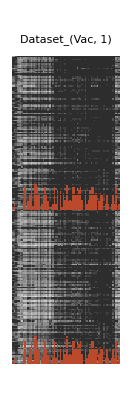
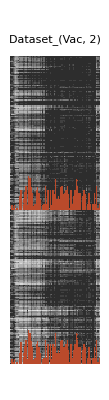
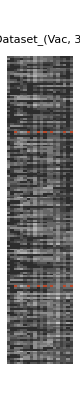
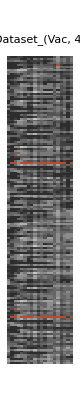
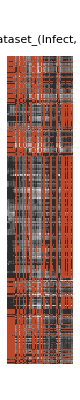
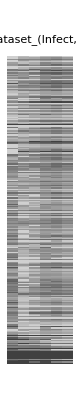
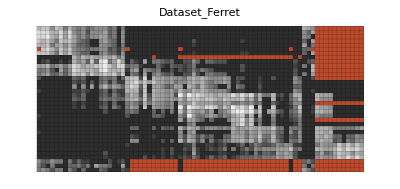

```mathematica
Append[Table[
plotData=N@Table[data[{virus,serum}],{serum,sera[table][[;;;;If[table==="Vinh",10,1]]]},{virus,viruses[table]}]/.val_Real:>Log10@val;
ArrayPlot[plotData,]
,{table,sortedTables}],]
```

#### Panel A: Prediction Scatter Plots

Below are scatter plots comparing the leave-one-out predictions to the actual measurements. In each plot, we combine the predictions from all viruses in one dataset and show the RMSE between the predictions and measurements (σ_Actual) and the mean estimated uncertainty of these predictions (σ_Predict).

Notes on the code [mouse-click to expand]:

Human vaccination datasets are shown in blue, human infection datasets in green, and the ferret infection dataset in orange

Predictions are shown as swarm plots, because the Fonville data takes on discrete values (5, 10, 20...)

Histograms show the distribution of actual error around the predicted value

Code takes ~1 minute to run, since we predict the behavior of every possible virus in each dataset (317 virus-dataset pairs resulting in 20,000 predictions)

To decrease file size, we use a trimmed forest with less accurate predictions [described in the Initialization section]

```mathematica
(* Predict values for each virus-dataset pair *)
predictionsLeaveOneOut=Association@Table[table->Join@@DeleteMissing[Table[completionPredictions[{virus,table}],{virus,viruses[table]}],2,All],{table,sortedTables}];
```

```mathematica
(* Plotting *)
plotLeaveOneOut=Table[
plotCompletion[predictionsLeaveOneOut[table],]
,{table,sortedTables}];
Rasterize@Grid[Partition[Flatten@plotLeaveOneOut,4,4,1,""],Spacings->{{3->3},2}]
```

-Graphics-

#### Panel B: Chord Diagram

We summarize the transferability between datasets using a chord diagram. For each arc connecting datasets X and Y, a larger width at the outer circle represents greater transferability. Notes on this code:

The chord connecting Study X and Study Y represent the 1/slope of the transferability function between both studies. The width of the chord as it approaches Study X represents 1/(f_(Y→X)) while the transferability as it approaches Study Y represents 1/(f_(X→Y))

Transferability is not symmetric between tables, and hence the two widths are generally different

Chords are only shown whenever there is meaningful transferability between studies (1/slope>=0.2)

Tables are labeled according to their original source [see the translation here]

Note that the Fonville Ferret Study is poorly predicted by all other tables, and hence it has no appreciable transferability

```mathematica
transferabilityLeaveOneOut=Clip[Threshold[Table[D[compareTables[tablePredictingFrom->tableToPredict],x]
,{tableToPredict,sortedTables},{tablePredictingFrom,sortedTables}]/.val_Real:>1/val,0.2],{0,1}];
chordDiagram[transferabilityLeaveOneOut,"Labels"->sortedTables,Sequence@@optsChordDiagram]
```

-Graphics-

#### [Extra Mathematica Figure] Expected Error

Given the ≈2-fold error of the HAI assay, we can computationally predict the distribution of measurements had each experiment been repeated. In other words, for all measurements with HAI=5, 10, 20... we multiply them by 2^𝒩 (equivalent to adding 𝒩 log_10 2 to the log-titer) where 𝒩 is a random variate from the standard normal distribution (mean zero and unit standard deviation; which corresponds to the 2-fold error of the assay).

The plots below show these hypothetical repeated measurements (blue) overlaid on our predictions of the data (black). In general, we find an excellent match for titers between 10 and 160. Our predictions for the lowest titers with HAI=5 are skewed upwards, since the data is censored (with measurements <5 reported as 5), and this censoring also distorts our predictions at the highest titers ≥320, where we tend to underestimate the true titers. More sophisticated methods that account for this censoring should better predict these large titer measurements.

```mathematica
SeedRandom[12345];
Table[
resRepeatedExperiment=Transpose[{ConstantArray[First@#,Last@#],Around[First@#+RandomVariate[NormalDistribution[],Last@#]Log10[2],Log10[2.]]}]&/@Sort@Tally[First/@predictionsLeaveOneOut[table]];
Show[First@plotCompletion[predictionsLeaveOneOut[table],IntervalMarkersStyle->None,PlotLabel->font[datasetLabel[table]],PlotStyle->GrayLevel/@Subdivide[7],"Radius"->0.015,"PlotType"->"Swarm","PlotEpilogPos"->{{-1,1},{-1,1}},ImageSize->200],First@plotCompletion[Join@@resRepeatedExperiment,IntervalMarkersStyle->None,PlotLabel->font[datasetLabel[table]],PlotStyle->{RGBColor[0.37240774720178266, 0.5096058607573024, 0.6389690923581445],RGBColor[0.45486803165305895, 0.5803583905017774, 0.6940838512413247],RGBColor[0.5372549534496341, 0.6470588603013963, 0.7490196230148063],RGBColor[0.6195525107061994, 0.7175810496189788, 0.803844874146865],RGBColor[0.7058479092773239, 0.7842621637952184, 0.8587719746815831],RGBColor[0.7882979058434185, 0.8549188289858504, 0.9137018917897248],RGBColor[0.8707832523912935, 0.9210835486125053, 0.9675377646708797]},"Radius"->0.015,"PlotType"->"Swarm","PlotEpilogPos"->{{-1,1},{-1,1}}]]
,{table,DeleteCases[sortedTables,"Vinh"]}]
```

### Figure 5: Leave-Multi-Out Analysis

In Figure 3, we showed that multiple viruses can be individually withheld and accurately predicted via matrix completion. Here, we demonstrate that a large set of 124 viruses can be simultaneously withheld and predicted.

We sought the minimal virus panel that could predict all remaining viruses with ≤4-fold error. There may be  many such minimal panels, and our procedure was to select viruses at random to withhold provided that σ_Predict≤4-fold for that virus and all other withheld viruses, stopping once there were no more candidates. See the Initialization section for details.

#### Panel A: Schematics of the Data

The schematics below depicts the 124 viruses [shown in gold] that we simultaneously withheld from the various datasets.

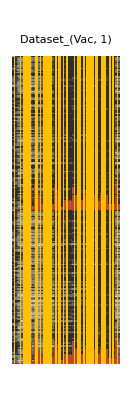
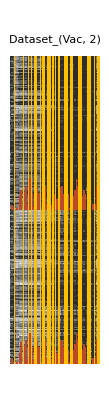
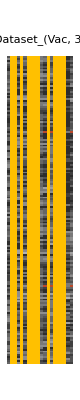
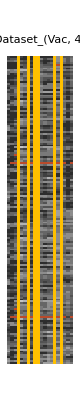
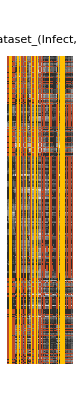
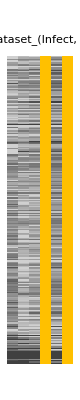
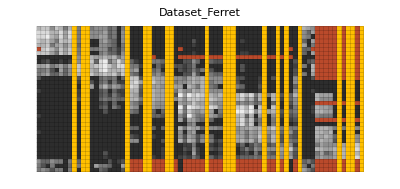

```mathematica
Append[Table[
plotData=N@Table[data[{virus,serum}],{serum,sera[table][[;;;;If[table==="Vinh",10,1]]]},{virus,viruses[table]}]/.val_Real:>Log10@val;
plotData[[All,Join@@Position[viruses[table],Alternatives@@Cases[virusesWithheldLeaveMultiOut,{virus_,table}:>virus]]]]=Missing["Withheld"];
ArrayPlot[plotData,]
,{table,sortedTables}],]
```

#### Panel A: Prediction Scatter Plots

As in Figure 3A, we show scatter plots comparing the leave-multi-out predictions to the actual measurements.

Note that in this leave-multi-out analysis, we simultaneously predict the 70,000 measurements from 124 viruses

In contrast, during leave-one-out analysis we only withhold a single virus, predicting far fewer measurements (on the order of hundreds)

Since we are using trimmed forests, we add the "MinPointsTransferability"→1 option to enable these predictions, even though there are very few decision trees to compute the transferability between studies. With the full forests, this option is not needed

```mathematica
(* Predict values for each virus-dataset pair *)
predictionsLeaveMultiOut=Association@Table[table->Join@@DeleteMissing[Table[completionPredictions[{virus,table},"ExtraWithheldViruses"->virusesWithheldLeaveMultiOut,"Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1,leaveMultiOutS3toS14},Join@@#&],Merge[{leaveOneOutVinh,leaveMultiOutVinh},Join@@#&]},"MinPointsTransferability"->1],{virus,Cases[virusesWithheldLeaveMultiOut,{virus_,table}:>virus]}],2,All],{table,sortedTables}];
```

```mathematica
(* Plotting *)
plotLeaveMultiOut=Table[
plotCompletion[predictionsLeaveMultiOut[table],]
,{table,sortedTables}];
Rasterize@Grid[Partition[Flatten@plotLeaveMultiOut,4,4,1,""],Spacings->{{3->3},2}]
```

-Graphics-

#### Panel B: Chord Diagram

As in Figure 3B, we summarize the transferability between datasets using a chord diagram. This diagram looks markedly different from the main text result because we used trimmed forests in this notebook.

```mathematica
transferabilityLeaveMultiOut=Clip[Threshold[Table[D[compareTables[tablePredictingFrom->tableToPredict,Cases[virusesWithheldLeaveMultiOut,{virus_,tablePredictingFrom|tableToPredict}:>virus],"Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1,leaveMultiOutS3toS14},Join@@#&],Merge[{leaveOneOutVinh,leaveMultiOutVinh},Join@@#&]},"MinPointsTransferability"->1],x]
,{tableToPredict,sortedTables},{tablePredictingFrom,sortedTables}]/.val_Real:>1/val,0.2],{0,1}];
chordDiagram[transferabilityLeaveMultiOut,Sequence@@optsChordDiagram]
```

-Graphics-

### Figure 6: Expanding Datasets

Here, we expand the Fonville and Vinh dataset as much as possible, predicting each of their sera against all 81 viruses that appears in these datasets. This expansion requires an additional random forest whose creation is described in the Initialization section.

#### Extending Vinh Data

The Vinh dataset reaps the greatest benefits from this expansion, since it contains many sera and few viruses. By predicting how the 25,000 Vinh sera inhibit 75 additional viruses, we predict 2,000,000 new measurements.

Note that we only load every 10th Vinh serum to increase the speed of these predictions, which is why the y-axis shows values that are 10x smaller than what we have in the manuscript [this can be undone in the Initialization section]

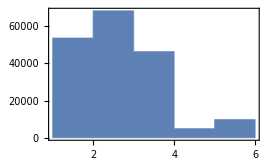

```mathematica
Histogram[Cases[Join@@Table[dataExpanded[{virus,serum}],{serum,sera["Vinh"]},{virus,viruses[All]}],around_Around:>Last@around],{1},]
```

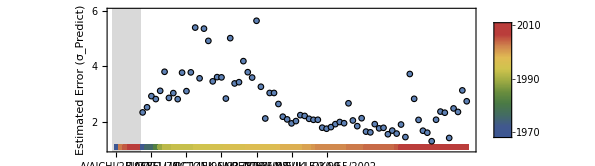

```mathematica
(* Sort viruses by their year of circulation *)
indexVirusesPredicted=DeleteCases[OrderingBy[viruses[All],virusYear],Alternatives@@Join@@Position[viruses[All],Alternatives@@viruses["Vinh"]]];
plotData=MapIndexed[{First@#2+6,#["Uncertainty"]}&,Table[dataExpanded[{virus,First@sera["Vinh"]}],{virus,viruses[All][[indexVirusesPredicted]]}]];
sortedViruses=Join[viruses["Vinh"]/.replaceVinhOriginalVirusNames,viruses[All][[indexVirusesPredicted]]];
(* Plotting *)
leg=BarLegend[{"DarkRainbow",{1968,2011}},ImageSize->150];
exportPlot=ListPlot[plotData,]
```

#### Extending Fonville Panel

The Fonville datasets can be similarly expanded to predict new virus behavior. To visualize these predictions, we show the schematics from Figure 3A, with measurements shown in gray and the predictions for the expanded virus panel colored according to the estimated uncertainty σ_Predict. Missing values that could not be inferred are shown in dark-red.

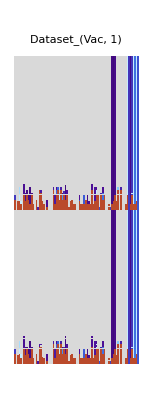
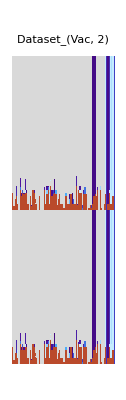
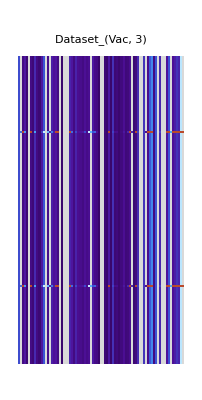
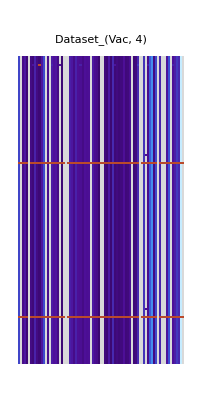
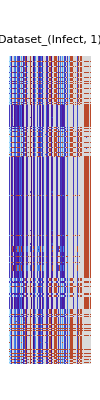
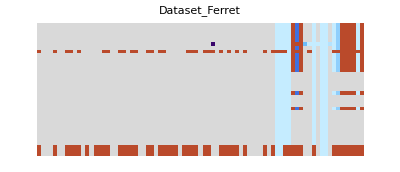
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  |  |  |

```mathematica
Grid[{Table[
plotData=Map[Which[
MatchQ[#,_Real],"Measured",
MatchQ[#,_Around],Log10@#["Uncertainty"],
True,Missing[]
]&,Table[dataExpanded[{virus,serum}],{serum,sera[table]},{virus,viruses[All]}],{2}];
ArrayPlot[plotData,]
,{table,DeleteCases[sortedTables,"Vinh"]}],Prepend[ConstantArray[SpanFromLeft,5],]},Spacings->1]
```

### Figure 7: Applications of Matrix Completion

We present a few potential applications using the expanded antibody-virus measurements, although we hope that this wealth of data will serve as the springboard for many additional forms of analysis.

#### Panel A: High-Resolution Antibody Response

Three examples of the expanded antibody response

Since we only load every 10th Vinh serum for speed, the Vinh landscape slightly differs although it shows the same trend. (If the full Vinh dataset were loaded, the 5th serum would show the response from the manuscript)

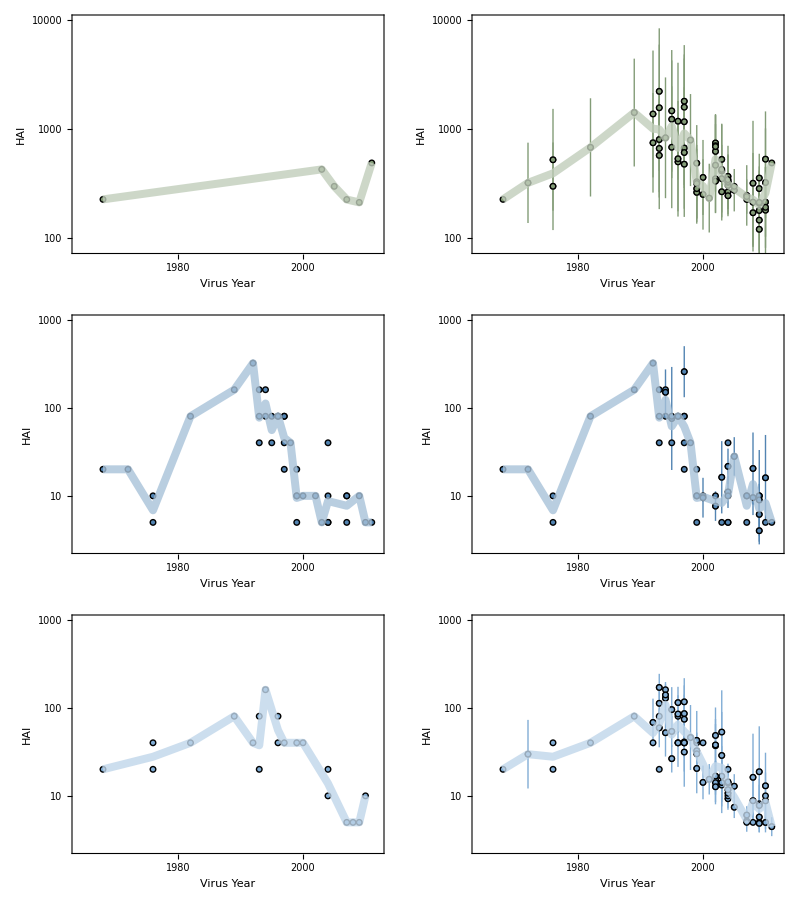

```mathematica
Block[{colors="Colors"/.optsChordDiagram},
Grid[MapIndexed[
Table[Show[showResponse[#,viruses[All],dataSource,"Color"->Switch[First@#2,
1,Darker[colors[[6]],0.2],
2,Darker[colors[[4]],0.15],
3,Darker[colors[[3]],0.05]
],If[#===sera["Vinh"][[5]],"YRange"->{80,10000},Sequence@@{}]]]
,{dataSource,{data,dataExpanded}}]&
,{sera["Vinh"][[5]],sera["S5"][[204]],sera["S13"][[1]]}],Spacings->{2,1}]
]
```

#### Panel B: Breadth vs Potency

For every possible range of years (e.g. 1968-1972 or 2005-2011), consider all viruses V within this range. The x-axis shows the (year of circulation of the most recent virus)-(year of circulation of the oldest virus). For each dataset, we compute the best lower bound (HAI_min) so that the HAI titer against every virus in V equals HAI_min or larger. In other words, a larger HAI_min represents a stronger response against all viruses in V

Since we only analyze every 10th Vinh serum, the HAI_min results here are slightly smaller than what is shown in the manuscript

```mathematica
(* Years of all viruses *)
virusYears=Union[virusYear/@viruses[All]];
(* Adding individual viruses within one year *)
virusYearRanges=Join[{#,#}&/@virusYears,Subsets[virusYears,{2}]];
(* Calculate best Subscript[HAI, min] for each table and each range of virus years *)
plotData=Association@Table[
table->Table[
virusSubset=Cases[viruses[All],virus_/;IntervalMemberQ[Interval@virusYearRange,virusYear@virus]];
titerBound=Max[Min/@(DeleteMissing[Table[dataExpanded[{virus,serum}],{serum,sera[table]},{virus,virusSubset}],1,All]/.Around[val_,_]:>val)];
If[NumericQ@titerBound,
{Subtract@@Reverse@MinMax[virusYear/@virusSubset],titerBound},
Nothing
]
,{virusYearRange,virusYearRanges}]
,{table,sortedTables}];
```

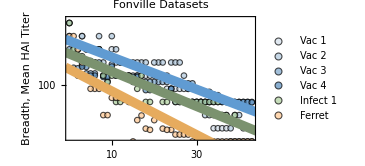
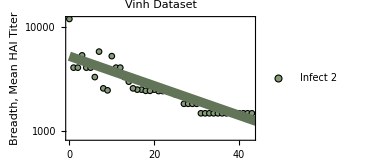
-Graphics- | -Graphics-

```mathematica
Grid[{{Show[
ListPlot[First/@(ReverseSortBy[#,Last]&/@GatherBy[#,First])&/@plotData/@sortedTables[[{1,2,3,4,5,7}]],],
Plot[{10^(3.-0.037x),10^(2.7-0.04x),10^(2.35-0.05x)},{x,-1,50},]
],Show[
ListPlot[First/@(ReverseSortBy[#,Last]&/@GatherBy[#,First])&/@plotData/@{"Vinh"},],
Plot[10^(3.715-0.0142x),{x,0,50},]
]}},Spacings->2]
```

#### Panel C: Pandemic Preparedness: New Variant Arises, Measured in 1 Dataset

H3N2 Perth 2009 is the most recent virus in the most recent dataset (Fonville S14). If this virus just emerged and was only measured in S14, could we predict its values in S13 to see whether those sera would also inhibit this new variant?

```mathematica
Grid[List@plotCompletion[completionPredictions[{"A/PERTH/16/2009","S13"},"OtherTables"->{"S14"}],],Spacings->{3}]
```

-Graphics-

### Figure S1: Transferability across Tables

Transferability maps between every pair of studies:

Plots are shown as simple, uncluttered scatter plots to focus the attention on the slope of the data. The x-axis (σ_Training) and y-axis (σ_Actual) are both linear and run from 0 to 1

For convenience, results are rasterized shrunk so that the can all be visualized simultaneously

```mathematica
Rasterize[Grid[Table[Replace[compareTables[tablePredictingFrom->tableToPredict,"ShowPlot"->True],_Missing->""]
,{tablePredictingFrom,sortedTables},{tableToPredict,sortedTables}]],ImageSize->300]
```

-Graphics-

### FIgure S2: Comprehensive Completion across Two Datasets

In Figure 2, we predicted values for three viruses from Table S13, S3, or S1 → Table S14. Here, we predict all other viruses between these datasets to demonstrate consistent prediction accuracy.

The discrepancy between the S1→S14 predictions and the SI figure is due to using trimmed forests with less accurate predictions [described in the Initialization section]

```mathematica
(* Leave-one-out analysis for each virus in Table S14 using Tables S13, S3, or S1 *)
{tableOfInterest,otherTables}={"S14",{"S13","S3","S1"}};
plotData=Table[
predictions=DeleteMissing[completionPredictions[{virusOfInterest,tableOfInterest},"OtherTables"->{tablePredictingFrom}],1,All];
σPredicted=Mean[(Last[#1]["Uncertainty"]&)/@predictions];
σActual=RootMeanSquare[((Subtract@@#1)["Value"]&)/@predictions];
{10^σPredicted,10^σActual}
,{tablePredictingFrom,otherTables},{virusOfInterest,viruses[tableOfInterest]}];
(* Clip values to lie between 0 to 10 (in our manuscript, this only clips 3 Subscript[σ, Predicted] values) *)
plotData=plotData/.val_Real:>Clip[val,{0,10}];
```

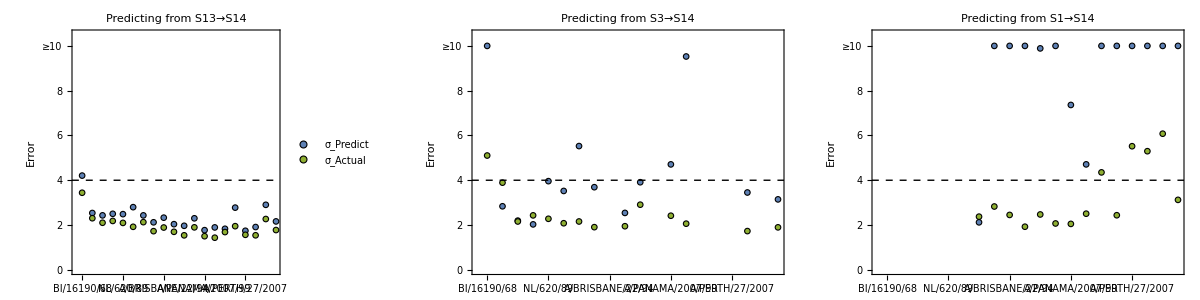

```mathematica
Grid[{MapIndexed[(
(* Viruses with no predictions are shown in gray *)
virusLabels=MapAt[font[#,LightGray]&,viruses[tableOfInterest],Position[plotData[[First@#2]],Except[{_?NumericQ..}],{1},Heads->False]];
(* Plot Subscript[σ, Predict] vs Subscript[σ, Actual] *)
ListPlot[Transpose[#][[All]],])&,plotData]},Spacings->2]
```

### Figure S3: Negative Control, Sequence Similarity

Can virus HA sequence similarity a “standard curve” between sequence relatedness and HAI? The resulting curve is highly inaccurate, generating an essentially flat response that does not capture the variance within the data.

Compute HA edit distance (ΔAA) to the vaccine strain

ΔAA is always calculated forward in time (i.e. log_10[(recent virus)/(older virus)] with viruses from the same year sorted alphabetically). This defines an ordering for any two viruses

We only use the four vaccine studies to give this algorithm the best chance to succeed (since our analysis showed that the infection and ferret datasets are even harder to predict)

Since Table S13 doesn’t include the vaccine strain A/Brisbane/10/2007 in the virus panel, we use A/Perth/27/2007 as a proxy (ΔAA_epitope=1,ΔAA_tot=3)

Compute the change in hemagglutination inhibition (ΔHAI) and relate it to ΔAA relative to the vaccine strain

```mathematica
(* HA edit distance *)
distSeq[virus1_,virus2_]:=EditDistance@@Replace[{virus1,virus2},replaceSeqFonville,{1}]
(* Vaccine strains *)
vaccine["S5"]="A/NANCHANG/933/95";
vaccine["S6"]="A/SYDNEY/5/97";
vaccine["S13"]="A/PERTH/27/2007";
vaccine["S14"]="A/PERTH/16/2009";
```

#### Panel A: Creating a Standard Curve between on Sequence Similarity

```mathematica
plotData=Join@@Table[Map[{distSeq@@#[[All,1]],#[[2,2]]-#[[1,2]]}&,DeleteMissing[Table[{{vaccine[table],Log10@N@data[{vaccine[table],serum}]},{virus,Log10@N@data[{virus,serum}]}},{serum,sera[table]},{virus,DeleteCases[SortBy[viruses[table],virusYear],vaccine[table]]}]/._data->Missing[],2,All],{2}],{table,{"S5","S6","S13","S14"}}];
Echo[Length[Join@@plotData],"# of virus-virus comparisons used to make standard curve:"];
```

# of virus-virus comparisons used to make standard curve:  34679

```mathematica
(* Average of ΔHA within 3 amino acids of each other *)
interpolateVac=Interpolation[Mean/@GatherBy[Join@@plotData,Floor[#[[1]]/3]&]];
interpolateUpperVac=Interpolation[{Mean@#[[All,1]],Mean@#[[All,2]]+StandardDeviation@#[[All,2]]}&/@GatherBy[Join@@plotData,Floor[#[[1]]/3]&]];
interpolateLowerVac=Interpolation[{Mean@#[[All,1]],Mean@#[[All,2]]-StandardDeviation@#[[All,2]]}&/@GatherBy[Join@@plotData,Floor[#[[1]]/3]&]];
(* Plotting *)
Rasterize@Quiet[Show[ListPlot[Join@@plotData,],Plot[{interpolateVac[x],interpolateUpperVac[x],interpolateLowerVac[x]},{x,2,75},]],InterpolatingFunction::dmval]
```

-Graphics-

#### Panel B: Leave-One-Out Analysis using Sequence Similarity

Using this standard curve, we carry leave-one-out analysis, repeating the analysis 10 times to avoid sampling bias.

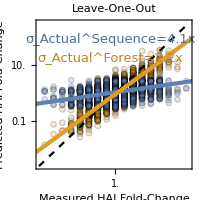

```mathematica
(* Predictions using sequence-based standard curve *)
SeedRandom[12345];
plotDataSeq=Join@@Table[
sample=RandomSample[Range@Length@plotData,Round[0.3Length@plotData]];
interpolateVac=Interpolation[Mean/@GatherBy[Join@@plotData[[sample]],Floor[#[[1]]/3]&]];
(* Predict response for the remaining samples *)
{#[[2]],Quiet[interpolateVac[#[[1]]],InterpolatingFunction::dmval]}&/@Join@@plotData[[Complement[Range@Length@plotData,sample]]]
,{iteration,10}];
(* Compare with predictions from the random forest model in Fig 4 *)
Do[
reference[table]=completionPredictions[{vaccine[table],table},"OtherTables"->{"S5","S6","S13","S14"},"Forest"->{leaveOneOutFonville,Automatic}]/.Around[val_,_]:>val
,{table,{"S5","S6","S13","S14"}}]
plotDataForest=Join@@Table[DeleteMissing[Join@@Table[(completionPredictions[{virus,table},"OtherTables"->{"S5","S6","S13","S14"},"Forest"->{leaveOneOutFonville,Automatic}]/.Around[val_,_]:>val)-reference[table],{virus,DeleteCases[viruses[table],vaccine[table]]}],1,All],{table,{"S5","S6","S13","S14"}}];
(* Plotting *)
fitForest=fitPerp[plotDataForest];
fitSeq=fitPerp[plotDataSeq];
Show[plot[{plotDataForest[[;;;;20]],plotDataSeq[[;;;;80]]},],Plot[{fitSeq,fitForest},{x,-3,3},PlotStyle->Thickness[0.015]]]
```

#### Panel C: Sequence Similarity within Datasets

When viruses are withheld in leave-one-out analysis, how similar is the nearest virus within this dataset? The results below compute the mean±standard deviation for all viruses in each study.

```mathematica
(* Virus list with Vinh name replacements *)
listVirusTable=Join@@(Tuples[{viruses@#,{#}}]&/@sortedTables);
(* Average ΔAA of withheld virus to nearest other virus within the same dataset *)
resLeaveOneOutSimilarity=Table[
virusesToConsider=DeleteDuplicates[First/@Cases[listVirusTable,{Except[First@entry],Alternatives@@DeleteCases[containingTables[First@entry],Last@entry]}]];
Append[entry,First@Nearest[(virusesToConsider/.replaceSeqFonville)->"Distance",First@entry/.replaceSeqFonville]]
,{entry,listVirusTable}];
showGrid@Prepend[{datasetLabel@#[[1,2]],Around[Mean[Last/@#],StandardDeviation[Last/@#]]}&/@GatherBy[resLeaveOneOutSimilarity,#[[2]]&],{"Dataset","Min ΔAA"}]
```

Dataset | Min ΔAA
Dataset_(Vac, 1) | 5.4.
Dataset_(Vac, 2) | 5.4.
Dataset_(Vac, 3) | 6.6.
Dataset_(Vac, 4) | 6.6.
Dataset_(Infect, 1) | 5.4.
Dataset_(Infect, 2) | 6.5.
Dataset_Ferret | 3.41.9

### Figure S4: Explaining the Chord Diagrams

We define the transferability between two datasets as 1/slope of the best-fit lines in Figure S1

Transferability is clipped to lie between 0 and 1, where 0 represents poor transferability and 1 represents two datasets with perfect transferability

```mathematica
transferabilityLeaveOneOut=Clip[Threshold[Table[D[compareTables[tablePredictingFrom->tableToPredict],x]
,{tableToPredict,sortedTables},{tablePredictingFrom,sortedTables}]/.val_Real:>1/val,0.2],{0,1}];
chordDiagram[transferabilityLeaveOneOut,"Interactive"->#,Sequence@@optsChordDiagram]&/@{{True,0},{True,4},False}
```

{-Graphics-,-Graphics-,-Graphics-}

### Figure S6: Leave-One-Out: Individual Vinh Results

In Figure 3A, we showed the cumulative results for all leave-one-out predictions in the Vinh study (Infection Dataset 2). Here, we plot the individual leave-one-out results for each of the six Vinh viruses.

```mathematica
(* Leave-one-out analysis for each Vinh virus *)
predictionsVinh=Association@Table[virus->DeleteMissing[completionPredictions[{virus,"Vinh"}],1,All],{virus,viruses["Vinh"]}];
```

```mathematica
(* Plotting *)
Grid[Partition[Flatten@MapIndexed[plotCompletion[predictionsVinh[#],]&,viruses["Vinh"]],4,4],Spacings->{{3->3},2}]
```

-Graphics-

### Figure S7: Visualizing the Expanded Datasets

We show all of the values in the expanded Fonville and Vinh datasets that can be predicted with ≤4-fold error. The Vinh predictions may look artificially different from the main text figure because sera are clustered based on their similarity, and the orders of clusters may change.

```mathematica
(* Virus labels with colors representing their year of circulation *)
virusLabels=Graphics[{MapIndexed[{{ColorData["DarkRainbow"][Rescale[virusYear@#,{1968.,2011}]],EdgeForm[{Thin,Black}],Rectangle[{First@#2,0},{First@#2+1,1}]},Text[font[Rotate[#,π/2],8],{First@#2+0.5,-0.2},{0,1}]}&,SortBy[viruses[All]/.virusNamesCorrections,virusYear]]},ImageSize->526.5,PlotRangePadding->None];
```

```mathematica
(* Fonville datasets - sera clustered by similarity within each dataset *)
expandedFonville=Table[
plotData=Table[dataExpanded[{virus,serum}],{serum,sera[table]},{virus,SortBy[viruses[All],virusYear]}]/.{Around[val_,uncertainty_]/;uncertainty<=4.:>val,Around[val_,uncertainty_]/;uncertainty>4.:>Missing[]}/.val_Real:>Log10@val;
If[table=!="S1",
(* Cluster all other data by serum similarity *)
orderedSera=Quiet[Dendrogram[plotData->sera[table],ClusterDissimilarityFunction->"Ward",ImageSize->Full][[1,2;;,1,1,1]],Dendrogram::mlemptyfeat];
plotData=plotData[[Ordering[sera[table]]]][[InversePermutation@Ordering[orderedSera]]]
];
ArrayPlot[plotData,]
,{table,DeleteCases[sortedTables,"Vinh"]}];
```

```mathematica
(* Vinh dataset (takes a minute to run) - sera clustered by similarity *)
plotData=Table[dataExpanded[{virus,serum}],{serum,sera["Vinh"]},{virus,SortBy[viruses[All],virusYear]}]/.{Around[val_,uncertainty_]/;uncertainty<=4.:>val,Around[val_,uncertainty_]/;uncertainty>4.:>Missing[]}/.val_Real:>Log10@val;
orderedSera=Quiet[Dendrogram[plotData->sera["Vinh"],ClusterDissimilarityFunction->"Ward",ImageSize->Full][[1,2;;,1,1,1]],Dendrogram::mlemptyfeat];
plotData=plotData[[Ordering[sera["Vinh"]]]][[InversePermutation@Ordering[orderedSera]]];
expandedVinh=ArrayPlot[plotData,];
```

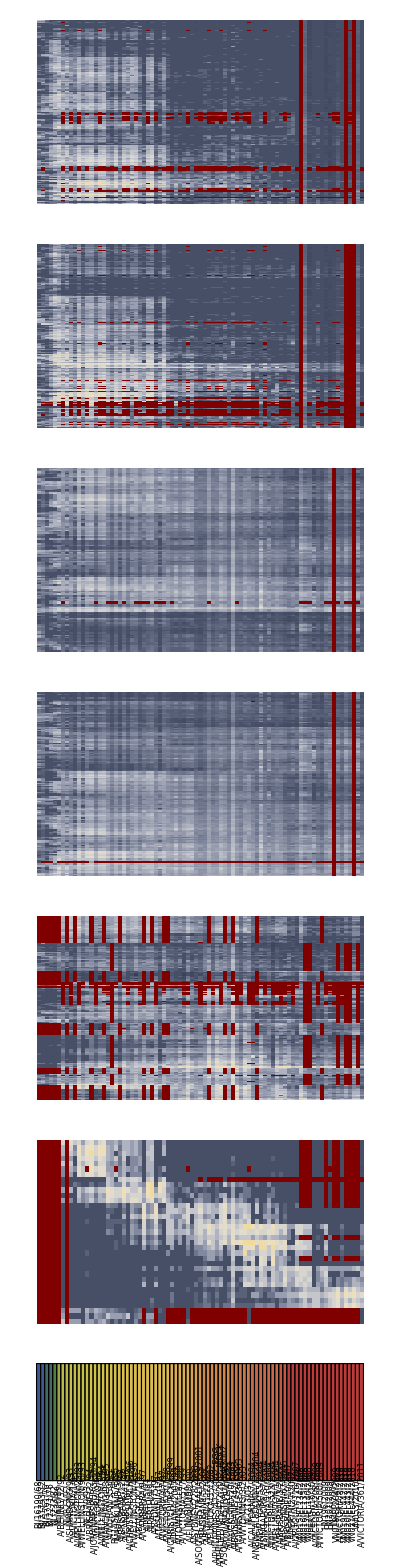
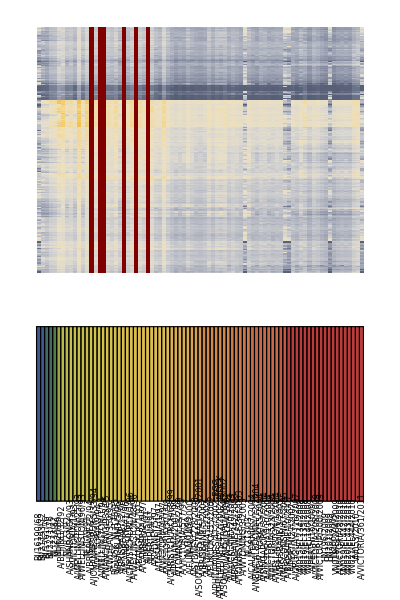
-Graphics- | 
-Graphics- |

```mathematica
(* Plotting *)
Grid[{{Column[Append[expandedFonville,virusLabels],Alignment->Right,Spacings->0.1],},
{Column[Append[{expandedVinh},Show[virusLabels,ImageSize->512]],Alignment->Right,Spacings->0],}}]
```

### Figure S8: Vinh-Like Expansions for Fonville Datasets

In the Vinh dataset, sera were measured against 6 viruses. Using the Fonville datasets, we predicted how each serum would inhibit the 75 additional Fonville viruses [see Figure 5]. Here, we demonstrate that these 6 viruses can predict the expanded virus panel by carrying out this same process for the Fonville datasets (Table S3, S5, and S6) that contain at least 5 Vinh viruses

We first grow the extra decision trees necessary to expand these datasets and then perform the predictions

Note that this is a harder problem, since the Vinh expansion could utilize these three Fonville studies, whereas in this case each study can only use the two other Fonville studies to perform the expansion

```mathematica
tablesOfInterest={"S5","S6","S3"};
(* List of all non-Vinh viruses in these Fonville tables that we will predict *)
virusesWithheldFonv=Join[Join@@Table[{#,table}&/@Complement[viruses[table],viruses["Vinh"]],{table,tablesOfInterest}],Join@@Table[{#,table}&/@viruses[table],{table,Complement[Append[fonvilleTables,"Vinh"],tablesOfInterest]}]];
```

#### Growing Extra Trees to Expand Tables S5/S6/S3

After we withhold all but the six Vinh viruses from a Fonville Study X (either S5, S6, or S3), we will use the remaining two studies to predict values for the remaining 75 Fonville viruses. This expansion requires two steps:

Quantify transferability: First, we compute the transferability from the two other studies to Study X (which now only contains 6 viruses). In other words, we perform leave-one-out analysis on each of these six viruses and use the remaining 5 viruses to infer its behavior, comparing σ_Training with σ_Actual

This requires growing a small forest between these three studies, using just the six Vinh viruses as features. Note that there is no point to quantifying the transferability using other viruses, since we only want to quantify the transferability to Study X, and not between the two remaining studies

This code takes ~1 minute to run

Predict expanded panel: We then grow another decision tree for each of the non-Vinh viruses in Study X that we want to predict using the other two studies

Again, the features used to predict each virus must be restricted to the 6 Vinh viruses, since that is the only data contained in Study X

This code takes several minutes to run, since we predict the 181 viruses in these three studies

Notes about the code:

The forests below use numTrees=10 for a fast implementation, but in the manuscript we used numTrees=50 to generate more precise predictions

```mathematica
(* Number of trees in the random forest *)
numTrees=10;
```

```mathematica
(* Quantify transferability *)
Do[
PrintTemporary["Starting Table "<>tableOfInterest];
forestCompareStudies[tableOfInterest]=Association@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
{virusOfInterest,tableOfInterest}->growTrees[virusOfInterest,tableOfInterest,"NumTrees"->numTrees,"ExtraWithheldViruses"->virusesWithheldFonv]
,{virusOfInterest,Intersection[viruses[tableOfInterest],viruses["Vinh"]]}];
,{tableOfInterest,tablesOfInterest}]
```

```mathematica
(* Predict expanded panel *)
Do[
PrintTemporary["Starting Table "<>tableOfInterest];
forestExpandStudies[tableOfInterest]=Association@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
(* Grow a forest of all potentially useful decision trees to expand Vinh panel *)
forest=growTrees[virusOfInterest,tableOfInterest,DeleteCases[tablesOfInterest,tableOfInterest],"NumTrees"->numTrees,"WithholdVirusOfInterest"->False,"ExtraWithheldViruses"->virusesWithheldFonv];
(* Prune forest to just the top 5 decision trees (the only ones that will be used) *)
{virusOfInterest,tableOfInterest}->Join@@(SortBy[#,#[[3]]&][[;;UpTo@5]]&/@GatherBy[forest,First])
,{virusOfInterest,Complement[viruses[tableOfInterest],viruses["Vinh"]]}]
,{tableOfInterest,tablesOfInterest}]
```

Once these forests have been grown, we can predict how the other 75 Fonville viruses should behave based solely upon measurements from the 6 Vinh viruses

```mathematica
Table[
(* Predict expansions for each table *)
predictingExpansion[tableOfInterest]=Table[
predictions=completionPredictions[{virusOfInterest,tableOfInterest},"Return"->"ExpandDataset","ExtraWithheldViruses"->virusesWithheldFonv,"Forest"->{Merge[{forestCompareStudies[tableOfInterest],forestExpandStudies[tableOfInterest]},Join@@#&],Automatic},"NumTopTrees"->50];
If[predictions==={},
Nothing,
measurements=Table[data[{virusOfInterest,serum}]/.val_Real:>Log10@val,{serum,sera[tableOfInterest]}];
plotData=DeleteMissing[Transpose@{measurements,predictions},1,All];
σPredicted=Mean[Last[#]["Uncertainty"]&/@plotData];
σActual=RootMeanSquare[(Subtract@@#)["Value"]&/@plotData];
{virusOfInterest,σPredicted,σActual}
]
,{virusOfInterest,Complement[viruses[tableOfInterest],viruses["Vinh"]]}];
(* Iconize output *)
Iconize[predictingExpansion[tableOfInterest],"Predictions for "<>tableOfInterest]
,{tableOfInterest,tablesOfInterest}]
```

#### Expanding Fonville Tables S3/S5/S6

```mathematica
(* Canned results from the previous section *)
{predictingExpansion["S5"],predictingExpansion["S6"],predictingExpansion["S3"]}={,,};
```

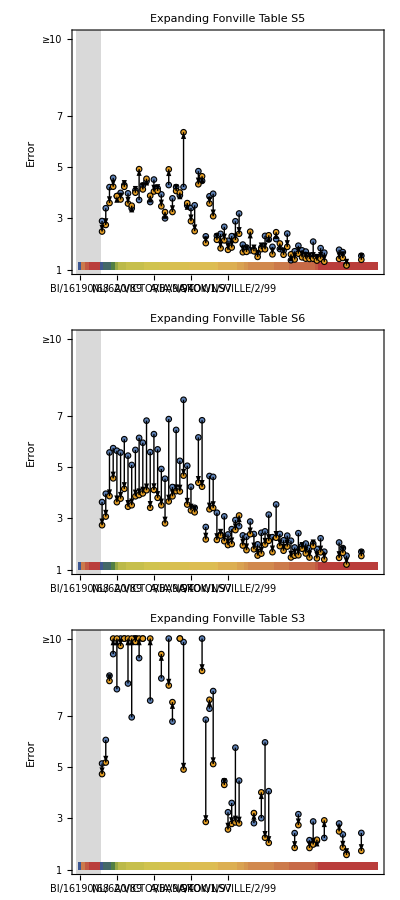

```mathematica
Grid[List/@Table[
(* Clip predictions with Subscript[σ, Predict]≥10-fold *)
predictionsSorted=predictingExpansion[tableOfInterest]/.val_Real:>Clip[val,{0,1}];
(* Order viruses by year of circulation *)
sortedViruses=Join[viruses["Vinh"],SortBy[DeleteCases[viruses[All],Alternatives@@viruses["Vinh"]],virusYear]];
plotDataσPredict=Transpose@{Range@Length@sortedViruses,10^sortedViruses/.Rule@@@predictionsSorted[[All,{1,2}]]};
plotDataσActual=Transpose@{Range@Length@sortedViruses,10^sortedViruses/.Rule@@@predictionsSorted[[All,{1,3}]]};
(* Plotting *)
ListPlot[{plotDataσPredict,plotDataσActual},]
,{tableOfInterest,tablesOfInterest}]
,Spacings->{2,2}]
```

### Figure S9: UMAP of Expanded Datasets

Using the expanded datasets, we can apply a UMAP and overlay the (unused) information about each virus’s year of circulation to examine whether the viruses evolve in time towards distinct patterns

UMAP options "NeighborsNumber"→20 and "MinDistance"->0.05 were chosen to roughly match the results in R. While there are clear differences between the two programming languages, there is still a temporal trend associated with virus year

Because we only use every 10th Vinh serum for speed, the Extended Vinh plot looks slightly different from what is shown in the manuscript

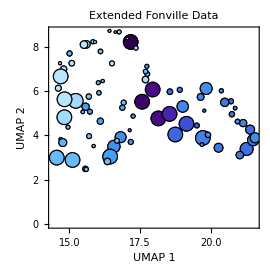
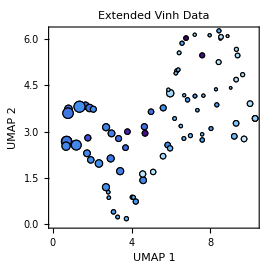
-Graphics- | -Graphics- |

```mathematica
Block[{expandedDataAssoc,plotData,uncertaintyRange={2,3,4,5}},
expandedDataAssoc=Association@{"Fonville"->Table[dataExpanded[{virus,serum}],{virus,SortBy[viruses[All],virusYear]},{serum,sera[All]}],"Vinh"->Table[dataExpanded[{virus,serum}],{virus,SortBy[viruses[All],virusYear]},{serum,sera["Vinh"]}]};
Grid[List@Append[Table[
plotData=DimensionReduce[expandedDataAssoc[dataset]/.Around[val_,_]:>val,2,Method->{"UMAP","NeighborsNumber"->20,"MinDistance"->0.05}];
ListPlot[List/@plotData,,
(* Color viruses according to their year of circulation *)
PlotStyle->(ColorData["DeepSeaColors"][Rescale[#,{1968,2011}]]&/@virusYear/@SortBy[viruses[All],virusYear]),
(* Larger size denotes a virus whose titers are more uncertain *)
PlotMarkers->plotMarker/@(FirstCase[#,Around[val_,uncertainty_]:>2uncertainty]&/@expandedDataAssoc[dataset]/.{val_Real:>Clip[val,{0,15}],_Missing:>0.01})]
,{dataset,{"Fonville","Vinh"}}],],Spacings->2]
]
```

### Figure S10: Nuclear Norm Minimization Asymmetry

A curious artifact of nuclear norm minimization is that even with noise-free data where each measurements has been seen before (i.e. a task that any human can solve with ease), missing values may not be perfectly recovered.

As a first example, consider the following simple dataset where each row represents an (x,y) pair. The simplest complete matrix (with the smallest matrix rank of 1) would fill in the bottom five rows identically to the top five rows. Yet, surprisingly, nuclear norm minimization fills these values in as (1,1), (2,2), (3,3), (4,4), and (5,5).

1 | 5
2 | 10
3 | 15
4 | 20
5 | 25
1 | *
2 | *
3 | *
4 | *
5 | *

The plots below show the more general case using the relationship y=m x, but with the same structure of missing values. This artifact appears for every choice of m>1.

```mathematica
Block[{range=Range@5,colorMeasured=RGBColor[0.7247058823529412, 0.7215686274509804, 0.7215686274509804],colorMissing=RGBColor[0.9, 0.6776470588235294, 0.]},
Grid[{Table[
dataPreCompletion=Join@@Prepend[ConstantArray[Transpose@{range,ConstantArray[Missing[],Length@range]},1],Transpose@{range,m range}];
dataPostCompletion=nuclearNormMinimization[dataPreCompletion,"ShiftType"->None];
fit=Fit[dataPostCompletion[[6;;10]],x,x];
Show[Plot[{x,m x,fit},{x,0,10},PlotLabel->font["y = "<>ToString@m<>"x"],],ListPlot[{dataPreCompletion[[;;5]],dataPostCompletion[[6;;10]]},]]
,{m,{5,2,1,0.5,0.2}}]},Spacings->1.5]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

This problem is exacerbated when the number of missing entries are repeated n times. When y=m x for m>1/(√n), values are incorrectly filled in as y=x/(√n) which decreases in accuracy for larger n. The plots below show the results of nuclear norm minimization when n=5.

```mathematica
Block[{range=Range@5,colorMeasured=RGBColor[0.7247058823529412, 0.7215686274509804, 0.7215686274509804],colorMissing=RGBColor[0.9, 0.6776470588235294, 0.]},
Grid[{Table[
dataPreCompletion=Join@@Prepend[ConstantArray[Transpose@{range,ConstantArray[Missing[],Length@range]},5],Transpose@{range,m range}];
dataPostCompletion=nuclearNormMinimization[dataPreCompletion,"ShiftType"->None];
fit=Fit[dataPostCompletion[[6;;10]],x,x];
Show[Plot[{x,m x,fit},{x,0,10},PlotLabel->font["y = "<>ToString@m<>"x"],],ListPlot[{dataPreCompletion[[;;5]],dataPostCompletion[[6;;10]]},]]
,{m,{5,2,1,0.5,0.2}}]},Spacings->1.5]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

We note that this behavior depends upon the type of centering performed prior to nuclear norm minimization, and it is completely alleviated if the data is either row- or column-centered. This suggests that when predicting the values for an entirely missing column (as in our leave-one-out analysis), nuclear norm implementations using row- or column-centering may result in substantially better results.

### Figure S11: Nuclear Norm Minimization with many Missing Values

Another surprising feature of nuclear norm minimization is that including “useless” viruses that have no overlapping data with a virus-of-interest may nevertheless result in substantially less accurate predictions.

Below, we look at one specific example from the Fonville datasets, where we predict virus V_0="VN018/EL204/2009", from Table S3→S1.

At first glance, this matrix completion should be highly accurate, since there are several viruses that have very similar titers to V_0 in both tables S1 and S3. Yet when we withhold V_0 and predict its titers via nuclear norm minimization using all Fonville viruses, the predictions are highly inaccurate (RMSE≈1)

A minimal example that shows these poor predictions can be carried out using the following viruses:

V_1="HN201/2009"

V_2="HN206/2009"

V_3="VN019/EL442/2010"

V_4="VN020/EL443/2010"

V_5="A/SINGAPORE/37/2004"

V_6="A/SOUTH_AUSTRALIA/53/2001"

V_7="A/SYDNEY/228/2000"

V_8="A/SOUTH_AUSTRALIA/84/2002"

V_1-V_4 [which we call the “good viruses”] show highly identical behavior to V_0 in both Tables S1 and S3, and matrix completing V_0 using these four viruses leads to accurate predictions, as expected

V_5-V_8  [which we call the “useless viruses”] were either not measured in Table S3 at all, or were only measured against complementary sera to V_0. In either case, any sensible matrix completion algorithm should not utilize their values to predict V_0 in Table S1. Unfortunately, nuclear norm minimization using V_1-V_8 results in very inaccurate predictions against V_0, demonstrating that this approach is waylaid when including viruses V_5-V_8

Unlike in Figure S8, where the artifact could be removed by row-centering, this artifact only occurs when data is row-centered prior to matrix completion. This suggests that one of these artifacts may be unavoidable when matrix completing across datasets using nuclear norm minimization

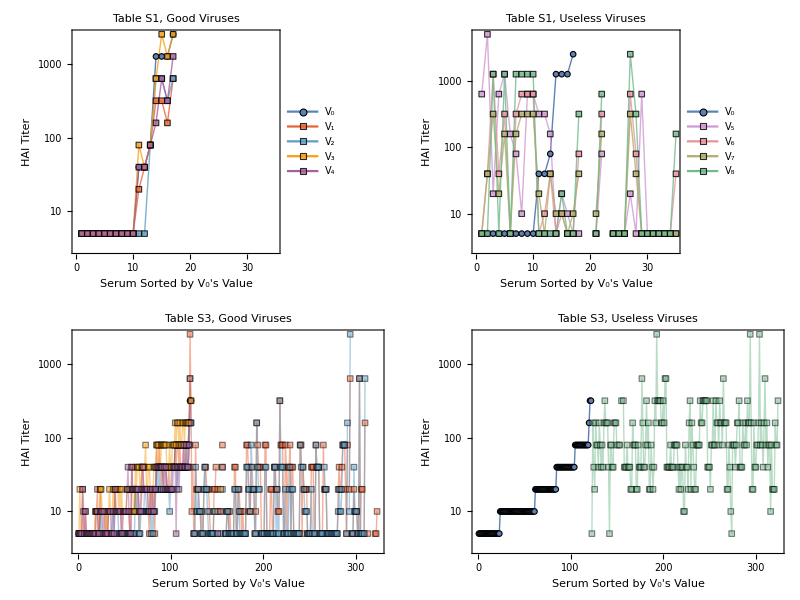

```mathematica
V0="VN018/EL204/2009";
goodViruses={"HN201/2009","HN206/2009","VN019/EL442/2010","VN020/EL443/2010"};
uselessViruses={"A/SINGAPORE/37/2004","A/SOUTH_AUSTRALIA/53/2001","A/SYDNEY/228/2000","A/SOUTH_AUSTRALIA/84/2002"};
{colorsGood,colorsUseless}={{RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.647624, 0.37816, 0.614037]},{RGBColor[0.8116708417619922, 0.6012303372612686, 0.8258504778335548],RGBColor[0.9085947212237386, 0.5752991583360579, 0.6133060580895009],RGBColor[0.6930195290945361, 0.6799726542041912, 0.4199367485764253],RGBColor[0.4508635801558966, 0.7307293561790306, 0.5496504597577443]}};
legend["Good"]=;
legend["Useless"]=;
Grid[Table[
ListPlot[
(* Sort sera by the measurements of Subscript[V, 0] *)
Table[data[{virus,serum}],{virus,Prepend[If[label==="Good",goodViruses,uselessViruses],V0]},{serum,SortBy[sera[table],data[{V0,#}]&]}],Joined->True,]
,{table,{"S1","S3"}},{label,{"Good","Useless"}}],Spacings->{2,2}]
```

Below are the results from nuclear norm minimization using either V_0-V_4 [left] or V_0-V_8 [right]. For efficiency, we perform this nuclear norm minimization using the RPCA algorithm which is much faster than standard nuclear norm minimization.

```mathematica
Clear[completeExample]
completeExample[listViruses_]:=Block[{virusOfInterest=V0,tableOfInterest="S1",tables={"S1","S3"},listSera},
listSera=Join@@sera/@tables;posWithheld=Tuples[Apply[Join,{Position[listSera,Alternatives@@sera[tableOfInterest]],Position[listViruses,virusOfInterest]},{1}]];dataMeasurements=N[Table[data[{virus,serum}],{serum,listSera},{virus,listViruses}]]/.{_data|_Missing->Missing[],val_Real:>Log10[val]};dataPreCompletion=ReplacePart[dataMeasurements,posWithheld->Missing["Withheld"]];dataPostCompletion=RPCA[dataPreCompletion,"ShiftType"->"RowCenter"];DeleteMissing[Transpose[{Extract[dataMeasurements,posWithheld],Extract[dataPostCompletion,posWithheld]}],1,All]
]
```

```mathematica
Grid[{Table[
(* Gather predictions by the discrete value of their true measurement *)
plotData=Sort/@SortBy[GatherBy[DeleteMissing[completeExample[Join[{V0},otherViruses]],1,All],First],#[[1,1]]&];
(* For aesthetic reasons only, help swarm plot collapse at the bottom-right (where predictions perfectly match data) *)
SeedRandom[12345];
plotData[[1,All,-1]]=plotData[[1,All,-1]]+RandomReal[{-0.1,0.1},Dimensions@plotData[[1,All,-1]]];
(* Plotting *)
{tick,tickFrac}={0.025,0.25};
σActual=RootMeanSquare[(Subtract@@#)&/@Join@@plotData];
Show[swarmPlot[plotData,0.055,PlotLabel->font["Predict V_0 using V_1-"<>If[otherViruses==goodViruses,"V_4","V_8"],14],],
Plot[{x},{x,0.5,3.5},PlotStyle->{Black,Dashed}]]
,{otherViruses,{goodViruses,Join[goodViruses,uselessViruses]}}]},Spacings->2]
```

-Graphics-

### Figures S12: Distribution of Viruses across Datasets

The distribution of viruses measured in each study.

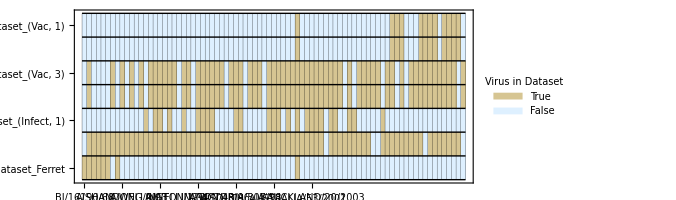

```mathematica
Block[{sortedViruses=SortBy[viruses[All]/.virusNamesCorrections,virusYear]},
ArrayPlot[Table[
Boole@MemberQ[viruses[table],virus]
,{table,sortedTables},{virus,sortedViruses}],ColorRules->{1->LightBlue,0->Darker[RGBColor[0.9333334830429179, 0.8588236087983301, 0.6352943119870211, 1.],0.1]},Frame->{True,True,False,False},Mesh->True,MeshStyle->{Black,Thickness[0.0005]},ImageSize->Full,FrameTicks->{MapIndexed[{First@#2,font@datasetLabel@#}&,sortedTables],MapIndexed[{First@#2,Rotate[font[#,10],π/2]}&,sortedViruses]},PlotRangePadding->None,PlotLegends->Placed[SwatchLegend[Automatic,font/@{True,False},LegendLabel->Placed[font["Virus in Dataset",14],Above],LegendFunction->frame],Above]]
]
```

# Initialization

## Plotting

### Plot Options

```mathematica
(* Map between internal dataset namesinfoTableNames and names in the manuscript *)
datasetLabel["S1"]="Dataset_Ferret";
datasetLabel["S3"]="Dataset_(Infect, 1)";
datasetLabel["S5"]="Dataset_(Vac, 1)";
datasetLabel["S6"]="Dataset_(Vac, 2)";
datasetLabel["S13"]="Dataset_(Vac, 3)";
datasetLabel["S14"]="Dataset_(Vac, 4)";
datasetLabel["Vinh"]="Dataset_(Infect, 2)";
```

```mathematica
(* Order of datasets in Figures 3 and 4 *)
sortedTables={"S5","S6","S13","S14","S3","Vinh","S1"};
```

```mathematica
(* Colors to denote missing or withheld values in the dataset schematics *)
{colorMissing,colorWithheld}={RGBColor[0.7294117486338101, 0.2901960661467868, 0.1686274028855742],RGBColor[0.9999999498892157, 0.752941171289242, 0.]};
```

```mathematica
(* Background colors in Figures 3 and 4 *)
backgroundColor[table_]:=Switch[table,
"S1",RGBColor[0.9764705579275531, 0.9058823723962381, 0.7803921721522492],
"S3"|"Vinh",RGBColor[0.8549019852367884, 0.94901961961848, 0.8549020442853469],
"S5"|"S6"|"S13"|"S14",RGBColor[0.8431371821797099, 0.9058824339626348, 0.9607843521075842]
]
```

```mathematica
(* Plot marker with dark edge *)
Options[plotMarker]={"Type"->"Circle","EdgeColor"->Black,"EdgeThickness"->Tiny};
plotMarker[size:(_Real|_Integer):0.04,opacity:(_Real|_Integer):1,OptionsPattern[]]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[OptionValue["EdgeThickness"]],OptionValue["EdgeColor"]}],Switch[OptionValue["Type"],
"Circle",Disk[],
"Square",Rectangle[]
]}],size};
```

```mathematica
(* Format String expressions *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Styling for plot legends *)
frame[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->White];
```

```mathematica
(* Show a number with 'digits' of precision past the decimal point *)
format[Missing[],_]:=Missing[]
format[num_,digits_:1]:=NumberForm[N@If[Abs@num<10^-digits/2,0,num],{digits+If[num>1,1,0],digits},NumberPadding->{"",If[num>10,"","0"]}]
format[GreaterThan[val_],digits_:1]:=Row[{">",format[val,digits]}]
format[LessThan[val_],digits_:1]:=Row[{"<",format[val,digits]}]
```

#### Fix Data when Plotting Log-Values

```mathematica
Clear[fixLogPlotting]
fixLogPlotting[val_?NumericQ]:=10.^val
fixLogPlotting[val_Around]:=Around[10.^(First@val),{10.^(First@val)-10.^(First@val-Last@val),10.^(First@val+Last@val)-10.^(First@val)}]
```

Example: Plotting these (logged) data points in log-space [top plot] and in un-logged space with log-axes [bottom]

```mathematica
(*plotData={{1,0.5},{2,Around[0.7,0.2]},{3,Around[0.6,0.3]},{4,0.4}};
ListPlot[plotData,PlotRange->{{0,5},{0,1}}]
ListPlot[MapAt[fixLogPlotting@#&,plotData,{All,2}],PlotRange->{{0,5},10^{0,1}},ScalingFunctions->"Log"]*)
```

### Plot with Aspect Ratio → 1

```mathematica
ClearAll[plot]
Options[plot]=Options@ListPlot;
SetOptions[plot,PlotMarkers->plotMarker[0.05,0.3],PlotRange->Automatic];
plot[data_,options:OptionsPattern[]]:=Block[{min,max,plotRange=OptionValue[PlotRange]},
{min,max}=MinMax[DeleteMissing[data,If[MatchQ[data,{{_?NumberQ,_?NumberQ}..}],1,2],All]/.Around[val_,_]:>val];
plotRange=If[plotRange===Automatic,
ConstantArray[{min,max},2],
Switch[plotRange,
{_Real|_Integer,_Real|_Integer},{plotRange,plotRange},
{range_List,range_List},plotRange,
_,Echo["PlotRange must match along x and y","Warning!"];Return[$Failed]]
];
Show[ListPlot[data,PlotRange->plotRange,options,ImageSize->270,AspectRatio->1,Frame->{True,True,False,False},FrameTicksStyle->12,PlotMarkers->OptionValue[PlotMarkers]],Plot[{x},{x,plotRange[[1,1]],plotRange[[1,2]]},PlotStyle->{{Black,Dashed}},Evaluate[Sequence@@DeleteCases[{options},HoldPattern[DataRange|InterpolationOrder|IntervalMarkers|IntervalMarkersStyle|Joined|LabelingFunction|MaxPlotPoints|MultiaxisArrangement|PlotMarkers|PlotLegends->_]]]]]
]
```

### Swarm Plot

```mathematica
(* https://mathematica.stackexchange.com/questions/42585/implementing-a-beeswarm-plot-in-mathematica *)intervalInverse[Interval[]]:=Interval[{-∞,∞}]
intervalInverse[Interval[int__]]:=Interval@@Partition[Replace[Flatten@{int},{
{-∞,mid___,∞}:>{mid},
{-∞,mid__}:>{mid,∞},
{mid__,∞}:>{-∞,mid},
{mid___}:>{-∞,mid,∞}
}],2]
intervalComplement[a_Interval,b__Interval]:=IntervalIntersection[a,intervalInverse@IntervalUnion@b]
```

```mathematica
(* 'data' is assumed to be a sorted vector of numbers *)
(* 'radius' specifies the distance between adjacent ponts *)
(* 'xShift' translates all points to the right *)
(* 'ratio' allows for arbitrary aspect ratios and plot ranges *)
(* 'fracOverlap' tunes how much points should overlap in the x-direction to make the map more compact (value should be between 0 and 1) *)
Clear[swarm]
swarm[data_,radius_,xShift_:0,ratio_:1.,fracOverlap_:0]/;0≤fracOverlap≤1:=Module[{points={},left,right,int},
Do[
int=Interval@@Cases[points,{x_,y_}/;(y/.Around[μ_,σ_]:>μ)>((pt/.Around[μ_,σ_]:>μ)- 2radius):>x+(1-fracOverlap)ratio{-1,1} Sqrt[(2radius)^2-(pt-y/.Around[μ_,σ_]:>μ)^2]];
right=Min@intervalComplement[Interval[{0,Infinity}],int];
left=Max@intervalComplement[Interval[{-Infinity,0}],int];
AppendTo[points,{If[right<-left,right,left],pt}]
,{pt,data}];
{xShift,0}+#&/@points
]
```

```mathematica
ClearAll[swarmPlot]
Options[swarmPlot]=Join[Options@Graphics,{PlotStyle->Automatic,PlotMarkers->Automatic,PlotLegends->None,IntervalMarkersStyle->Opacity[0.8]}];
SetOptions[swarmPlot,Frame->True];
SetOptions[swarmPlot,FrameTicks->{None,Automatic}];

(* Handle Missing values *)
swarmPlot[data_,radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]/;MemberQ[data,_Missing,All]:=swarmPlot[DeleteCases[data,{_,_Missing}|_Missing,All],radius,opts]

(* Single dataset without x-coordinates *)
swarmPlot[data_?(VectorQ[#,NumericQ@#||MatchQ[#,_Around]&]&),radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=swarmPlot[{{1,#}&/@data},radius,opts]
(* Single dataset with x-coordinates *)
swarmPlot[data_?(MatrixQ[#,NumericQ@#||MatchQ[#,_Around]&]&)/;Equal@@First/@data,radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=swarmPlot[{data},radius,opts]
(* Multiple datasets without x-coordinates *)
swarmPlot[data:{__?(VectorQ[#,NumericQ@#||MatchQ[#,_Around]&]&)},radius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=swarmPlot[MapIndexed[Thread@{First@#2,#}&,data],radius,opts]

(* Multiple datasets with x-coordinates *)
swarmPlot[data:{__?(MatrixQ[#,NumericQ@#||MatchQ[#,_Around]&]&)},pointRadius:(_?NumericQ|Automatic):Automatic,fracOverlap:(_Real|_Integer):0,opts:OptionsPattern[]]:=
Block[{intervalMarkers=OptionValue[IntervalMarkersStyle],plotStyle=OptionValue[PlotStyle],plotLegends=OptionValue[PlotLegends],aspectRatio=OptionValue[AspectRatio],plotRange=OptionValue[PlotRange],plotRangeRatio,colors,radius=pointRadius,plot,plotData},
(* Quality checks *)
If[!And@@(Equal@@First/@#&/@data),Echo["Dataset indices not uniform","Error!"];Break[]];

(* Radius selection *)
If[radius===Automatic,
radius=2 Mean[Join@@Differences/@Sort/@data[[All,All,-1]]];
If[MatchQ[radius,_Around],radius=radius["Value"]]
];

(* PlotRange *)
If[plotRange===Automatic,plotRange={{First@#-1,Last@#+1}&[MinMax@data[[All,1,1]]],MinMax@data[[All,All,2]]}
];
plotRangeRatio=Divide@@Subtract@@@plotRange;
If[aspectRatio===Automatic,aspectRatio=1/plotRangeRatio];

(* PlotStyle *)
colors=
Switch[plotStyle,
Automatic,ColorData[97]/@Range@Length@data,
_List,Join@@ConstantArray[plotStyle,Length@data],
_RGBColor|_GrayLevel,ConstantArray[plotStyle,Length@data],
_,plotStyle/@Range@Length@data
];
If[intervalMarkers===Opacity[0],intervalMarkers=None];

(* Plotting *)
plot=Graphics[{EdgeForm[{Thickness[Tiny],Black}],
MapIndexed[{
colors[[First@#2]],
plotData=swarm[Sort[Last/@#],radius,#[[1,1]],plotRangeRatio aspectRatio,fracOverlap];
(* Error bars *)
If[intervalMarkers=!=None,
{intervalMarkers,Line[{{#1[[1]],#1[[2]]["Value"]-#1[[2]]["Uncertainty"]},{#1[[1]],#1[[2]]["Value"]+#1[[2]]["Uncertainty"]}}]&/@Cases[plotData,{_,_Around}]},
{}
],
Disk[#1/.Around[μ_,σ_]:>μ,0.95 radius{plotRangeRatio aspectRatio,1}]&/@plotData}&,data]},Sequence@@DeleteCases[{opts},HoldPattern[IntervalMarkersStyle->_]],Frame->OptionValue[Frame],FrameTicks->OptionValue[FrameTicks]];
Switch[plotLegends,
(* No legend *)
None,plot,
(* Labels of legend provided *)
_List,Grid[{{plot,PointLegend[colors,plotLegends]}},Spacings->2],
(* Complete legend provided *)
_,Grid[{{plot,plotLegends}},Spacings->2]
]
]
```

```mathematica
(*(* Example of how you can manipulate the plot range and aspect ratio. The size of the circles will adjust to accomodate *)
pnts=;
{swarmPlot[pnts,0.012,PlotRange->{{0.5,2.5},{0,1.3}},ImageSize->250],swarmPlot[pnts,0.012,PlotRange->{{0.5,2.5},{0,1.3}},ImageSize->250,AspectRatio->1]}
(* Example of how you can tune the amount of overlap in the x-direction to make the plot more compact *)
swarmPlot[pnts,0.012,#,PlotRange->{{0.5,2.5},{0,1.3}},ImageSize->200,AspectRatio->1]&/@{0,0.3,0.6}*)
```

```mathematica
(*(* Example data *)
SeedRandom[12345];
data1=RandomVariate[ExponentialDistribution[1],200];
data2=RandomVariate[NormalDistribution[2,1],200];
(* Plot 1 or 2 daasets *)
plot1=swarmPlot[data1];
plot2=swarmPlot[MapIndexed[Thread@{2First@#2,#}&,{data1,data2}]];
(* Change the color while keeping the radius selection automatic *)
plot3=swarmPlot[{data1,data2},Automatic,PlotStyle->ColorData[95]];
(* Specify the circle radius explicitly in plot coordinates *)
plot4=swarmPlot[data2,0.2,ImageSize->200];
Grid[{{plot1,plot2,plot3,plot4}},Spacings->3]*)
```

### Chord Diagram

```mathematica
(* Options for chord diagram *)
optsChordDiagram={"Labels"->sortedTables,"Colors"->{RGBColor[0.8705884492036204, 0.9215685952074308, 0.9686275222610606],RGBColor[0.7421568051701294, 0.8431372794491305, 0.9343137183420358],RGBColor[0.5343136031701521, 0.7156863062682228, 0.8808823453306758],RGBColor[0.37745084697453624, 0.6098039138673352, 0.8215686424143651],RGBColor[0.756, 0.9, 0.6839999999999999],RGBColor[0.6426000000000001, 0.765, 0.5813999999999999],RGBColor[1, 0.9, 0.8]},"BackgroundOpacity"->0.7};
```

```mathematica
Clear[poincareArc,ribbon]
poincareArc[l0_List,nPts_:50]:=Module[{l=Sort[l0],dt,t,t1,t2,r,R,c},
dt=Abs[l[[1]]-l[[2]]];
If[dt>π,l=Sort[l+{0,-2π}]];
dt=Abs[l[[1]]-l[[2]]];
t=Plus@@l/2;
If[dt==Pi,{{Cos[l[[1]]],Sin[l[[1]]]},{Cos[l[[2]]],Sin[l[[2]]]}},
c={Cos[t],Sin[t]};
r=Tan[dt/2];
R=Sec[dt/2];
t1=ArcTan@@({Cos[l[[2]]],Sin[l[[2]]]}-R c);
t2=ArcTan@@({Cos[l[[1]]],Sin[l[[1]]]}-R c);
If[t2<t1,t2+=2π];
(r{Cos[#],Sin[#]})+(R c)&/@Subdivide[t1,t2,nPts]
]]
dist[{x1_,y1_,x2_,y2_},{u_,v_}]:=Max[Norm[{u,v}-{x1,y1}],Norm[{u,v}-{x2,y2}]];
ribbon[subPartitionAngles_,cols_,nPts_:50][a_,b_]:=Block[{θ1=subPartitionAngles[[a,b]],θ2=subPartitionAngles[[b,a]],pacs,circle1,circle2,coordinates,pnt1,pnt2,primitives,curve,vertexColors},
pacs=poincareArc/@Transpose@{θ1,Reverse[θ2]};
circle1={Cos[#],Sin[#]}&/@Subdivide[θ1[[1]],θ1[[2]],nPts] ;
circle2=DeleteDuplicates[{Cos[#],Sin[#]}&/@Subdivide[θ2[[1]],θ2[[2]],nPts] ];
coordinates=Join@@{pacs[[1]],circle1,pacs[[2]],circle2};
{pnt1,pnt2}=Median/@{circle1,circle2};
vertexColors=Blend[{cols[[a]],cols[[b]]},Norm[#-pnt1]/(Norm[#-pnt1]+Norm[#-pnt2])]&/@coordinates;
Polygon[coordinates,VertexColors->vertexColors]
]
```

```mathematica
(* https://resources.wolframcloud.com/FunctionRepository/resources/ChordDiagram/https://resources.wolframcloud.com/FunctionRepository/resources/ChordDiagram/Nonehttps://resources.wolframcloud.com/FunctionRepository/resources/ChordDiagram/HyperlinkActionRecycledHyperlinkActive *)
ClearAll[chordDiagram]
Options[chordDiagram] ={"Labels"->Automatic,"Colors"->Automatic,"BackgroundOpacity"->0.25,"Interactive"->False,"ShowCircleOutline"->False,"MaxRadius"->1.15,"TotalWidth"->18.5,ImageSize->200};
chordDiagram[matrix_,OptionsPattern[]]:=Block[{
interactive=OptionValue["Interactive"],rMax=OptionValue["MaxRadius"],
totalWidth=OptionValue["TotalWidth"],
Δθ,base,labels,cols,wedgesWidth,angles,wedges,innerCircle,subPartitionAngles,nonzeroPositions,backgroundChords,names,dynamicLabels,lessOpaque,index},

labels=If[OptionValue["Labels"]===Automatic,Range@Length[matrix],OptionValue["Labels"]];
cols=If[OptionValue["Colors"]===Automatic,ColorData[97]/@Range@Length[labels],OptionValue["Colors"]];

wedgesWidth=Clip[Total/@matrix,{0.1,∞}];
Δθ=(totalWidth-Total@wedgesWidth)/(Length@matrix);
angles=Partition[2π Rescale@Accumulate[Join[{0},Riffle[wedgesWidth,Δθ],{Δθ}]],2];
wedges=Thread[{cols,Annulus[{0,0},{1,rMax},#]&/@angles}];
innerCircle=Thread[{Darker[cols,0.05],Circle[{0,0},0.985,#]&/@angles}];
subPartitionAngles=Table[RotateRight[Partition[Rescale[Accumulate[Prepend[RotateLeft[matrix[[jj]],jj-1],0]],{0,wedgesWidth[[jj]]},Reverse@angles[[jj]]],2,1],jj-1],{jj,Length@matrix}];
nonzeroPositions=Position[matrix,Except[0|0.],{2},Heads->False];
backgroundChords={Opacity[OptionValue["BackgroundOpacity"]],ribbon[subPartitionAngles,cols]@@@DeleteDuplicates[Sort/@nonzeroPositions]};
lessOpaque=backgroundChords/.Opacity[a_]:>Opacity[OptionValue["BackgroundOpacity"]0.25];

labels=Switch[interactive,
False,
(* Static labels *)Table[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],{i,Length@labels}],
True,
(* Dynamic labels upon mouseover *)
Table[Mouseover[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],
{Text[Rotate[font[labels[[i]],14,Bold],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],
{White,Disk[{0,0},0.99]},lessOpaque,{Opacity[1],ribbon[subPartitionAngles,cols]@@@Select[nonzeroPositions,#[[1]]==i&]}}
],{i,Length[labels]}],
{True,_},
index=Last@interactive;
If[index==0,
Join[Table[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],{i,Length[labels]}],{{White,Disk[{0,0},0.99]},lessOpaque}],
ReplacePart[Table[Text[Rotate[font[labels[[i]],14],If[π<Mean@angles[[i]],Mean@angles[[i]]+π/2,Mean@angles[[i]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[i]]],Sin[Mean@angles[[i]]]}],{i,Length[labels]}],
index->{If[Length@labels>=index,Text[Rotate[font[labels[[index]],14,Bold],If[π<Mean@angles[[index]],Mean@angles[[index]]+π/2,Mean@angles[[index]]-π/2]],Mean[{1,rMax}]{Cos[Mean@angles[[index]]],Sin[Mean@angles[[index]]]}],{}],
{White,Disk[{0,0},0.99]},lessOpaque,{Opacity[1],ribbon[subPartitionAngles,cols]@@@Select[nonzeroPositions,#[[1]]==index&]}}
]
]
];

base=If[OptionValue["ShowCircleOutline"],{LightGray,Circle[{0,0},1],Circle[{0,0},rMax]},{}
];
Graphics[{base,backgroundChords,innerCircle,wedges,labels},PlotRange->(rMax){{-1,1},{-1,1}},ImageSize->OptionValue[ImageSize]]
]
```

### Visualizing the Antibody Response

```mathematica
ClearAll[showResponse]
Options[showResponse]={"Return"->"Plot","Color"->ColorData[97][1],"ColorHighlight"->Lighter@Purple,"YRange"->{2.5,1000}};
showResponse[serum_,listVirusesFull_List:viruses[All],dataSource_Symbol:dataExpanded,OptionsPattern[]]:=Block[{listViruses,listSera,color=OptionValue["Color"],colorHighlight=OptionValue["ColorHighlight"],plotData,plotDataAvg,valsAround},
listViruses=DeleteCases[listVirusesFull,virus_/;MatchQ[dataSource[{virus,serum}],_Missing|_data]];
plotData=Table[{virusYear@virus,dataSource[{virus,serum}]},{virus,SortBy[listViruses,virusYear]}];
(* Transform to log-space and remove points with uncertainty >4-fold *)
plotData[[All,2]]=plotData[[All,2]]/.val_Real:>Log10@val;
plotData=DeleteCases[plotData,{_,Around[_,uncertainty_]}/;uncertainty>Log10[4.]];
(* Average over multiple virus measurements in any year *)
plotDataAvg=GeometricMean/@GatherBy[Clip[plotData/.Around[val_,_]:>val,{0,∞}],First];
Switch[OptionValue["Return"],
"Response",plotData,
"AverageResponse",plotDataAvg,
"Plot",
Show[
valsAround=Cases[plotData,{year_,Around[val_,_]}:>{year,val}];
ListPlot[If[valsAround=!={},MapAt[fixLogPlotting@#&,valsAround,{All,2}],{}],PlotStyle->colorHighlight,PlotMarkers->plotMarker[1.6 0.07],FrameTicksStyle->12,Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"Virus Year","HAI"}),FrameStyle->Directive[Thickness[0.004],GrayLevel[0.3]],FrameTicks->,ScalingFunctions->"Log",PlotRange->{{1964,2012},OptionValue["YRange"]},PlotRangeClipping->False,ImageSize->250],
ListPlot[MapAt[fixLogPlotting@#&,plotData,{All,2}],PlotStyle->color,PlotMarkers->plotMarker[1.6 0.05,"EdgeThickness"->0.05],PlotRangeClipping->False,IntervalMarkers->"Bars",ScalingFunctions->"Log"],
ListPlot[MapAt[fixLogPlotting@#&,plotDataAvg,{All,2}],Joined->True,PlotStyle->Directive[Lighter[color,0.5],Opacity[0.8],Thickness[0.023]],PlotRange->All,ScalingFunctions->"Log"]]
]
]
```

### Formatted Grid

```mathematica
Options[showGrid]=Join[{"Header"->"Top",Dividers->Automatic},FilterRules[Options@Grid,Except[Dividers]]];
showGrid[data_,opts:OptionsPattern[]]:=Block[{header=OptionValue["Header"],dividers=OptionValue[Dividers],tan=Darker[RGBColor[1., 0.956, 0.876],0.05]},
If[dividers===Automatic,
dividers={{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Left"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{RGBColor[0.75, 0.75, 0.75]},RGBColor[0.2, 0.2, 0.2]},{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Top"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{False},RGBColor[0.2, 0.2, 0.2]}}
];
If[!MemberQ[{"Top","TopLeft","Left",None},header],Echo["Option 'Header' does not have appropriate form","Error!"];Return[$Failed]];
Grid[Map[If[MatchQ[#,_String|_Real|_Integer|_Row|_GreaterThan|_LessThan|_NumberForm],font@#,#]&,data,{2}],Background->{{If[MemberQ[{"TopLeft","Left"},header],tan,None]},{If[MemberQ[{"TopLeft","Top"},header],tan,Nothing],{White,GrayLevel[0.9400000000000001]}}},Dividers->dividers,If[Length@{opts}>=1,Sequence@@FilterRules[{opts},Options@Grid],Sequence@@{}]]
]
```

## Importing Data

#### Helper Functions

```mathematica
(* Number of Fonville tables containing a virus *)
containingTables[virus_]:=Cases[fonvilleTables,table_/;MemberQ[viruses[table],virus]]
(*(* Example Usage *)
containingTables/@viruses[All]*)
```

```mathematica
(* Fraction of variance explained via Pearson's correlation coefficient squared *)
Clear[correlation]
correlation[data_/;MatchQ[Min[StandardDeviation/@Transpose@data],0|0.]]:=Missing[]
correlation[data_]:=(Correlation@@Transpose@data)^2
```

```mathematica
(* Coefficient of determination R^2 *)
rSquared[data_]:=Module[{mean=Mean[data[[All,2]]]},
1-Total[(#[[1]]-#[[2]])^2&/@data]/Total[(#[[2]]-mean)^2&/@data]
]
```

```mathematica
(* Determine the year of isolation of a virus *)
(* When multiple strains have the same sequence (and hence their names are concatenated with a ";"), take the max year of circulation over all viruses *)
Clear[virusYear]
virusYear[str_String/;!StringContainsQ[str,";"]]:=Module[{year=StringDelete[Last@StringSplit[str,"/"],"_MDCK"|"_EGG"|"-egg"]},
Which[
StringMatchQ[year,DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter],ToExpression@year,

StringMatchQ[year,DigitCharacter~~DigitCharacter]&&ToExpression@year<50,
ToExpression@year+2000,

StringMatchQ[year,DigitCharacter~~DigitCharacter]&&50≤ToExpression@year<100,
ToExpression@year+1900,

True,
$Failed
]
]
```

```mathematica
(* Fit based on minimizing the perpendicular distance to the best-fit line *)
fitPerp[fitData_,showLineQ_:True]:=Block[{n=Length@fitData,xAvg=Mean@N@fitData[[All,1]],yAvg=Mean@N@fitData[[All,2]],B,b,a,numerator,denominator},
numerator=(Total[fitData[[All,2]]^2]-n yAvg^2)-(Total[fitData[[All,1]]^2]-n xAvg^2);
denominator=n xAvg yAvg-Total[Times@@@fitData];
If[denominator==0.,Return[$Failed]];
B=1./2 numerator/denominator;
b=-B+Sqrt[B^2+1];
a=yAvg-b xAvg;
If[showLineQ,
(* Return best-fit line *)
a+b x,
(* Return RMSE around best-fit line *)
Sqrt@Mean[(fitData[[All,2]]-(a+b fitData[[All,1]]))^2/(1+b^2)]
]
]
```

### Fonville 2014

Importing data from Fonville 2014: Antibody landscapes after influenza virus infection or vaccination

Table S1: This is the transpose of the original Fonville Table S1, so that the first column represents sera and the first row represents viruses. All other tables were already ordered in this format, so their un-transposed versions are imported.

Some viruses with the same name are labeled with underscores in Table S1 but forward slashes in the other tables, and we unify their names upon import ("HN196_2009"→"HN196/2009")

We also unified names that used short virus names in some tables but long virus names in other tables ("JO/33/94"→"A/JOHANNESBURG/33/94")

We fixed the typo “A/SHANGDONG/9/93”→“A/SHANDONG/9/93”

Tables S5-S6, S13-S14: The pre-vaccination and post-vaccination sera are distinguished by either having "_Pre" or "_Post" at the end of the serum name

All sera have their Table designation (either S1, S3, S5, S6, S13, or S14) in their name as "_TableX"

```mathematica
(* List of all Fonville supplementary tables *)
fonvilleTables={"S1","S3","S5","S6","S13","S14"};
```

```mathematica
Block[{rawData,table},
MapIndexed[(
rawData=#;
table=fonvilleTables[[First@#2]];
sera[table]=rawData[[2;;,1]];
viruses[table]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
)&
,]
];
```

The following contain a cumulative list of all viruses and sera in the Fonville datasets

```mathematica
(* Combined viruses and sera in all Fonville tables *)
sera[All]=Join@@sera/@fonvilleTables;
viruses[All]=Sort@DeleteDuplicates[Join@@viruses/@fonvilleTables];
(* Slight aesthetic reordering *)
viruses[All]=ReplacePart[viruses[All],
{21->viruses[All][[22]],
22->viruses[All][[21]],
41->viruses[All][[42]],
42->viruses[All][[41]]
}
];
```

```mathematica
(* HA Sequences *)
replaceSeqFonville=;
```

#### Corrections to Virus Names

Below is a comprehensive list of the changes we made from the original Fonville 2014 SI file in order to unify virus names and correct for potential mistakes:

Some viruses were written in shorthand in some tables and longhand in others. We unified all of them as follows:

FU/411/02 → A/FUJIAN/411/2002

JO/33/94 → A/JOHANNESBURG/33/94

NA/933/95 → A/NANCHANG/933/95

PM/2007/99 → A/PANAMA/2007/99

SD/9/93 → A/SHANDONG/9/93

WU/359/95 → A/WUHAN/359/95

Some viruses had mistakes in their virus names:

A/SHANGDONG/9/93 → A/SHANDONG/9/93 [Typo in city name, Shangdong does not exist]

A/PHILIPPINES/427/2002_MDCK→A/PHILIPPINES/472/2002_MDCK [According to Accession ID, the 427 strain number should be 472; this number also make more sense given the additional virus in the dataset called A/PHILIPPINES/472/2002_EGG]

To unify formatting, underscores were replaced by slashes:

HN196_2009 → HN196/2009

HN201_2009 → HN201/2009

HN206_2009 → HN206/2009

VN015_EL134_2008 → VN015/EL134/2008

VN016_EL135_2008 → VN016/EL135/2008

VN017_EL140_2008 → VN017/EL140/2008

VN018_EL204_2009 → VN018/EL204/2009

VN019_EL442_2010 → VN019/EL442/2010

VN020_EL443_2010 → VN020/EL443/2010

VN021_EL444_2010 → VN021/EL444/2010

VN053_2010 → VN053/2010

Prototype was removed from the Netherlands viruses, which were written using the shorthand NL:

Prototype_RG145K_A/NETHERLANDS/178/95 → RG145K_NL/178/95

Prototype_WT_A/NETHERLAND/179/93 → NL/179/93

Prototype_WT_A/NETHERLANDS/213/03 → NL/213/03

Prototype_WT_A/NETHERLANDS/301/99 → NL/301/99

Table S1 sera: Every serum name X was renamed to Serum_X_TableS1. In addition, we changed X in the following two cases to ensure that all virus names are uniformly capitalized and to fix the Shangdong typo

A/Nanchang/933/95 → A/NANCHANG/933/95

A/SHANGDONG/9/93 → A/SHANDONG/9/93

Table S3 sera: The Subject Number and Sample Year were combined and appended with _TableS3. For example, Subject 1 in Year 2007 became Subject1Year2007_TableS3

Table S5 and S6 sera: The Subject Number and Age were combined and appended with either _TableS5 or _TableS6. Following that, each sample was split into two sera, one containing the pre-vaccination titers (appended with _Pre) and the other with post-vaccination titers (appended with _Post). As an example from Table S5, Subject 258 with Age 29 resulted in Subject258Age29_TableS5_Pre and Subject258Age29_TableS5_Post

Table S13 and S14 sera: The Subject Number was appended with either _TableS13 or _TableS14. Following that, each sample was split into two sera, one containing the pre-vaccination titers (appended with _Pre) and the other with post-vaccination titers (appended with _Post). As an example from Table S13, Subject A028 resulted in SubjectA028_TableS13_Pre and SubjectA028_TableS13_Post

```mathematica
virusNamesCorrections={
(* Based on the virus name in the Accession IDs:"A/Philippines/427/2002_MDCK" in Fonville Tables S1,S3,S5,S6,S9 should be "A/Philippines/472/2002_MDCK" *)
"A/PHILIPPINES/427/2002_MDCK"->"A/PHILIPPINES/472/2002_MDCK"};
```

### Vinh 2021

Importing data from Vinh 2021: Age-seroprevalence curves for the multi-strain structure of influenza A virus

We only consider the six H3N2 viruses, since all viruses in Fonville 2014 are H3N2

The following 4/6 viruses exactly match to the Fonville strains:

Vinh H3-2003 (H3N2 A/Wyoming/3/2003) → Fonville H3N2 A/Wyoming/3/2003

Vinh H3-2005 (H3N2 A/Wisconsin/67/2005) → Fonville H3N2 A/Wisconsin/67/2005

Vinh H3-2007 (H3N2 A/Brisbane/10/2007) → Fonville H3N2 A/Brisbane/10/2007

Vinh H3-2011 (H3N2 A/Victoria/361/2011) → Fonville H3N2 A/Victoria/361/2011

The other 2/6 viruses have close homologues in the Fonville panel, so we match them up accordingly:

Vinh H3-1968 (H3N2 A/Aichi/2/1968) → Fonville A/Bilthoven/16190/1968 [differs by 3 amino acids in HA]

Vinh H3-2009 (H3N2 A/Victoria/210/2009) → Fonville A/Hanoi/EL201/2009 [differs by 7 amino acids in HA]

To speed up Initialization, we only consider every Δserum=10 sera in the Vinh dataset (resulting in 2,440 sera instead of 24,402 sera). To use the full Vinh dataset, rerun the code below with Δserum=1 in the top line

```mathematica
Block[{rawData=,Δserum=10},
rawData=rawData[[;;;;Δserum]];
(* Load the viruses/sera from the first row/column *)
sera["Vinh"]=rawData[[2;;,1]];
viruses["Vinh"]=rawData[[1,2;;]];
(* Import values in the form: data[{virus,antibody}] *)
Do[
data[{rawData[[1,indexVirus]],rawData[[indexAb,1]]}]=rawData[[indexAb,indexVirus]]
,{indexAb,2,First@Dimensions@rawData},{indexVirus,2,Last@Dimensions@rawData}]
];
```

```mathematica
(* For presentation purposes only *)
replaceVinhOriginalVirusNames={"BI/16190/68"->"A/AICHI/2/1968","HN201/2009"->"A/VICTORIA/210/2009"};
```

## Matrix Completion

### Random Forest Algorithm for Matrix Completion Across Datasets

#### Growing Decision Trees

Grow a decision tree that predicts values for virusOfInterest from otherTables->tableOfInterest

Options are shown below [mouse-click to expand]:

"NumVirusesForTraining": Number of other viruses used to train the decision tree and predict the values of the virusOfInterest. These viruses are bootstrap sampled (with replacement)

"MinumumNumViruses": The minimum number of overlapping viruses between the otherTables and the tableOfInterest necessary to train decision trees

"MinFracMeasurements": Minimum fraction of measurements necessary for each virus in one of the otherTables in order for it to be a viable candidate as a feature to predict the virusOfInterest. This ensures that the algorithm will learn patterns among actual data and not between missing values

"NumTrees": Number of decision trees to train from each of the otherTables

"FracSeraForTraining": The decision tree is trained using this fraction of sera in the otherTables and then cross-validated using the remaining sera to compute its RMSE σ_Training

"TrainingSampling": How to choose among the sera in the training set based on their titer against the virus-of-interest

Automatic: Uses {"InverseBinsSpecified",bins} for the discrete Fonville data and "Uniform" for the continuous Vinh data

"Uniform": Randomly sample sera

"Inverse": Only possible when measurements take discrete values. Randomly samples each serum with probability 1/count[titer] so that rarer values (often at the extremes) get sampled with equal frequency. This can be more susceptible to outliers, but it also partially helps prevent "drooping" predictions at the extreme values

{"InverseBinsSpecified",bins_List}: Similar to "Inverse", but with specified bins. For example, if there are few titers≥320, you can group these together into a single bin using bins=Log10@N@{{5},{10},{20},{40},{80},{160},{320,640,1280,2560,5120}} to prevent skewing the sampling towards bins with very few measurements

"WithholdVirusOfInterest": If True, withholds values for the virusOfInterest (as is done for the leave-one-out and leave-multi-out analyses). Otherwise, use all available data (as is done when expanding datasets)

"ExtraWithheldViruses": A list with elements {virus,table} specifying that data from this virus-table pair should be withheld. This is used in our leave-multi-out analysis, where we grow a forest that specifically excludes 124 withheld viruses

"SeedRandom": Controls the random selection to make the code reproducible

```mathematica
(* Default sampling bins for Fonville data *)
$bins=Log10@N@{{5},{10},{20},{40},{80},{160},{320,640,1280,2560,5120}};
```

```mathematica
ClearAll[growTrees]
Options[growTrees]={"NumVirusesForTraining"->5,"MinumumNumViruses"->5,"MinFracMeasurements"->0.8,"NumTrees"->50,"FracSeraForTraining"->0.3,"WithholdVirusOfInterest"->True,"ExtraWithheldViruses"->{},"SeedRandom"->12345};
growTrees[virusOfInterest_,tableOfInterest_,otherTables:(_List|All):All,OptionsPattern[]]:=Block[{withholdQ=OptionValue["WithholdVirusOfInterest"],seedRandom=OptionValue["SeedRandom"],numFeatures=OptionValue["NumVirusesForTraining"],
minFeatures=OptionValue["MinumumNumViruses"],
numSamples=OptionValue["FracSeraForTraining"],minFracMeasurements=OptionValue["MinFracMeasurements"],numTrees=OptionValue["NumTrees"],
extraWithheldViruses=OptionValue["ExtraWithheldViruses"],
listSera,listViruses,subsetTestingFull,subsetTrainingFull,subsetTraining,subsetTesting,subsetCrossValidate,posMissingTraining,posMissingTesting,posMissingCrossValidate,shiftTraining,shiftTesting,shiftCrossValidate,features,trainingIndex,predict,predictTesting,otherTable,trainingSampling,weights,bins},
(* Make predictions using all other tables containing virus *)
Join@@Table[
SeedRandom[seedRandom];
(* Only consider sera in Other Table measured against the Virus-of-Interest *)
listSera=Cases[sera[otherTable],serum_/;NumberQ@data[{virusOfInterest,serum}]];
(* Viruses in both tables *)
listViruses=DeleteCases[Intersection@@(DeleteCases[viruses[#],Alternatives@@Cases[extraWithheldViruses,{virus_,#}:>virus]]&/@{tableOfInterest,otherTable}),virusOfInterest];
(* Only consider viruses where most values are measured and not missing *)
listViruses=Cases[listViruses,virus_/;((Length@DeleteMissing@#)/Max[Length@#,1]>=minFracMeasurements&[Table[data[{virus,serum}],{serum,listSera}]])];
(* Add the virus of interest in front. Ensure there are enough viruses to create a forest *)
listViruses=Prepend[listViruses,virusOfInterest];
If[Length@listViruses<minFeatures,
Nothing,
(* Create the training and testing subsets *)
(* When expanding all tables, exclude testing subset *)
{subsetTrainingFull,subsetTestingFull}=(N@Table[data[{virus,serum}],{serum,#},{virus,listViruses}]&/@{listSera,If[withholdQ,sera[tableOfInterest],{}]}/.{_data|_Missing->Missing[],val_Real:>Log10@val});

(* Quality check: Inverse sampling is only possible for binned data (in Fonville) and not for continuous data (in Vinh) *)
trainingSampling=OptionValue["TrainingSampling"];
Which[
trainingSampling===Automatic&&otherTable==="Vinh",trainingSampling="Uniform",
trainingSampling===Automatic&&otherTable=!="Vinh",trainingSampling={"InverseBinsSpecified",$bins}
];
If[otherTable==="Vinh"&&trainingSampling=!="Uniform",PrintTemporary["Switching to uniform sampling for Vinh"];trainingSampling="Uniform"];

(* Make multiple decision trees with random subsets of feature/training examples *)
Table[
features=RandomChoice[Range[2,Length@listViruses],numFeatures];
weights=Switch[trainingSampling,
(* Random sampling across sera in training set *)
"Uniform",ConstantArray[1,Length@subsetTrainingFull[[All,1]]],
(* Sampling with weight 1/frequency so that every x-value gets equal weight *)
"Inverse",
subsetTrainingFull[[All,1]]/.Rule@@@MapAt[1/#&,Tally@subsetTrainingFull[[All,1]],{All,2}],
(* Sampling with weight 1/frequency with specified bins so that large-and-infrequent values (e.g. 1280, 2560) can be grouped together to mitigate outliers from destroying predictions *)
{"InverseBinsSpecified",_List},
bins=Last@trainingSampling;
subsetTrainingFull[[All,1]]/.DeleteDuplicates[Join@@Map[Thread[#->1/(Length@#)]&,Gather[subsetTrainingFull[[All,1]],Position[bins,#1][[1,1]]==Position[bins,#2][[1,1]]&]]]
];
trainingIndex=RandomChoice[weights->Range@Length@subsetTrainingFull,Round[numSamples Length@subsetTrainingFull]];
subsetTraining=subsetTrainingFull[[trainingIndex,Prepend[features,1]]];
(* Row-centering using unique features *)
posMissingTraining=Position[subsetTraining,_Missing,{2},Heads->False];
shiftTraining=Replace[Mean/@DeleteMissing/@Rest/@subsetTrainingFull[[trainingIndex,Prepend[Union@features,1]]],_Mean->0,{1}];
subsetTraining=ReplacePart[subsetTraining-shiftTraining,posMissingTraining->Missing[]];

(* Ensure that each feature has at least one non-Missing value *)
If[Cases[Transpose@subsetTraining[[All,2;;]],{_Missing..}]=!={},
Nothing,
predict=Predict[subsetTraining[[All,2;;]]->subsetTraining[[All,1]],Method->"DecisionTree",TrainingProgressReporting->None];

(* When withholding Virus-of-Interest (to validate method), create testing subset in Table-of-Interest *)
If[withholdQ,
subsetTesting=subsetTestingFull[[All,Prepend[features,1]]];
posMissingTesting=Position[subsetTesting,_Missing,{2},Heads->False];
shiftTesting=Replace[Mean/@DeleteMissing/@Rest/@subsetTestingFull[[All,Prepend[Union@features,1]]],_Mean->0,{1}];
subsetTesting=ReplacePart[subsetTesting-shiftTesting,posMissingTesting->Missing[]];
(* Apply decision tree to testing data, predict withheld value *)
(* Note: Based on minimal testing, predictions work just as well when some of the values in the testing dataset are Missing, so the ReplacePart below could be removed *)
predictTesting=ReplacePart[predict[subsetTesting[[All,2;;]]],Position[subsetTesting[[All,2;;]],_Missing,{2},Heads->False][[All,{1}]]->Missing[]];
];

(* If withholding Virus-of-Interest, check there is at least 1 testable prediction *)
If[withholdQ&&DeleteMissing[Transpose@{predictTesting,subsetTesting[[All,1]]},1,All]==={},
Nothing,
(* {Other Table, 
Viruses (features) used for training in Other Table, 
Cross-validation RMSE against unused serum samples in Other Table, 
If withholding, true RMSE in Table-of-Interest (not used for Virus-of-Interest),
either predictions or Decision Tree} *)
{otherTable,
listViruses[[features]],
(* Row-center cross-validation sera, compute RMSE *)
subsetCrossValidate=subsetTrainingFull[[Complement[Range@Length@subsetTrainingFull,trainingIndex],Prepend[features,1]]];
posMissingCrossValidate=Position[subsetCrossValidate,_Missing,{2},Heads->False];
shiftCrossValidate=Replace[Mean/@DeleteMissing/@Rest/@subsetTrainingFull[[Complement[Range@Length@subsetTrainingFull,trainingIndex],Prepend[Union@features,1]]],_Mean->0,{1}];
subsetCrossValidate=ReplacePart[subsetCrossValidate-shiftCrossValidate,posMissingCrossValidate->Missing[]];
RootMeanSquare[predict[subsetCrossValidate[[All,2;;]]]-subsetCrossValidate[[All,1]]],
(* Note: Cannot subtract predictTesting-subsetTesting[[All,1]], since cases where both are Missing[] would yield 0. This is not a concern for subsetTraining above, since by construction its first column is non-Missing *)
If[withholdQ,RootMeanSquare[Subtract@@@DeleteMissing[Transpose@{predictTesting,subsetTesting[[All,1]]},1,All]],Missing["NoTestingSubset"]],
(* Predict function *)
predict}
]
]
,{numTree,numTrees}]
]
,{otherTable,Which[
otherTables===All,DeleteCases[containingTables@virusOfInterest,tableOfInterest],
True,otherTables]}]
]
```

```mathematica
Clear[rowCenteredData]
rowCenteredData[listViruses_,tableOfInterest_]:=Block[{subset,posMissing,posUnique,shift},
subset=N@Table[data[{virus,serum}],{serum,sera[tableOfInterest]},{virus,listViruses}]/.{_data|_Missing->Missing[],val_Real:>Log10@val};
posMissing=Position[subset,_Missing,{2},Heads->False];
(* In case there are duplicate features, only row-center over unique features *)
posUnique=DeleteDuplicates[FirstPosition[listViruses,#][[1]]&/@listViruses];
shift=Replace[Mean/@DeleteMissing/@subset[[All,posUnique]],_Mean->0,{1}];
(* Return {row-centered data, row-centering shift} *)
{ReplacePart[subset-shift,posMissing->Missing[]],shift}
]
```

#### Quantifying Transferability across Tables

The transferability f_(X→Y) between Study X and Study Y is computed in a data-driven manner by plotting σ_Training vs σ_Actual using the non-withheld data. The trend between the best decision trees (with the lowest σ_Training) is characterized using linear regression to determine f_(X→Y). With this function, we estimate σ_Actual as f_(X→Y)(σ_Training)

The virusesWithheld parameter specifies a list of withheld viruses whose data should not be utilized in this analysis. This means that we remove predictions for these viruses from the σ_Training vs σ_Actual plot, and in addition we exclude any decision trees that use these viruses as a feature to predict any other virus

```mathematica
ClearAll[compareTables]
Options[compareTables]={
(* When True, outputs a plot of Subscript[σ, Training] vs Subscript[σ, Actual]. Otherwise output the transferability map (i.e. the best-fit line to these data) *)
"ShowPlot"->False,
(* Number of best trees to use from each leave-one-out analysis *)
"NumTopTrees"->10,
(* Random forest to use for {Fonville, Vinh} *)
"Forest"->{Automatic,Automatic},
(* Minimum # of points needed to compute transferability between two tables *)
"MinPointsTransferability"->5};
compareTables[tablePredictingFrom_->tableToPredict_,virusesWithheld:_List:{},OptionsPattern[]]:=Block[{forest=OptionValue["Forest"],virusOfInterest,tableOfInterest,pairedTablePredictions,predictionOOBerror,predictions,measurements,predictionTrueError,plotData,fit,intercept},

(* Set up the random forest of decision trees *)
forest=If[tableToPredict==="Vinh",
If[MatchQ[forest,Automatic|{_,Automatic}],
leaveOneOutVinh,
If[!MatchQ[forest,{_,_}],Echo["Option 'Forest' should have the forest for {Fonville,Vinh}","Error!"]];
Last@forest
],
If[MatchQ[forest,Automatic|{Automatic,_}],
leaveOneOutFonville,
If[!MatchQ[forest,{_,_}],Echo["Option 'Forest' should have the forest for {Fonville,Vinh}","Error!"]];
First@forest
]
];

plotData=Table[
{virusOfInterest,tableOfInterest}=entry;
pairedTablePredictions=SortBy[Cases[forest@{virusOfInterest,tableOfInterest},{tablePredictingFrom,viruses_,_?NumericQ,_?NumericQ,__}/;!ContainsAny[viruses,virusesWithheld]],#[[3]]&][[;;UpTo@OptionValue["NumTopTrees"],{3,4}]]
,{entry,Cases[Keys@forest,{Except[Alternatives@@virusesWithheld],tableToPredict}]}];
(* When there are enough measurements to make it possible, restrict attention to the top-5 best decision trees *)
If[Total[Length/@plotData]>300,plotData=plotData[[All,;;UpTo@5]]];
plotData=Join@@plotData;
(* Only compute transferability if there are at least 'MinPointsTransferability' points available (relevant for leave-multi-out) *)
If[Length@plotData<=OptionValue["MinPointsTransferability"],Return[Missing[]]];
(* In addition to the best-fit (perpendicular line) relating OOB error to the True RMSE, we also add the RMSE deviation of the fit-points, since some of the nearly-vertical lines could otherwise incorrectly predict very small errors *)
fit=fitPerp[plotData];
fit=fit+RootMeanSquare[(fit/.x->#[[1]])-#[[2]]&/@plotData];
If[D[fit,x]<0.5,(*Echo[fit,Row[{"Warning! Relation between Tables ",tablePredictingFrom->tableToPredict," (withholding ",virusesWithheld,") has small slope!"}]]*)
Return[Missing[]]];
If[OptionValue["ShowPlot"],
Show[
intercept=x/.First@Solve[fit==0,x];Show[ListPlot[plotData/.{}->{-10,-10},PlotLabel->font[Row[{tablePredictingFrom,"→",tableToPredict}]/.Append[Thread[fonvilleTables->{"Ferret","Infect 1","Vac 1","Vac 2","Vac 3","Vac 4"}],"Vinh"->"Infect 2"],14],]],
If[0<intercept<1,
Graphics[{Lighter@ColorData[97][1],Thickness[0.04],JoinForm["Round"],Line[{{0,0},{intercept,intercept},{1,fit/.x->1}}]}],
Plot[fit,{x,0,1},PlotStyle->{Lighter@ColorData[97][1],Thickness[0.04]}]
],
Plot[x,{x,0,1},PlotStyle->{{Black,Dashed}}]],
fit
]
]
```

#### Predicting Virus Behavior

Master function to predict values for a virusOfInterest in a tableOfInterest. Options are collapsed below:

The option "Return" can take on three values: "TitersAndError", "Error", or "ExpandDataset"

"Return"->"TitersAndError" implies that both the titer±uncertainty should be returned for the virusOfInterest in the tableOfInterest, along with the measurements for comparison. This is used in leave-one-out analysis and in leave-multi-out analysis to quantify the accuracy of our predictions

"Return"->"Error" only returns the uncertainty. This is used to generate the additional random forest in leave-multi-out analysis, and can also be used to determine how measuring an additional virus would change the uncertainty of dataset expansion

"Return"->"ExpandDataset" is used when predicting new virus behavior. It functions similarly to the "TitersAndError" option value, except that we do not include the measurements for the virusOfInterest (since these measurements may not exist when we expand a virus panel), and moreover we do not withhold values for the virusOfInterest

```mathematica
ClearAll[completionPredictions]
Options[completionPredictions]={
(* Which other studies should be used to predict virus behavior *)
"OtherTables"->All,
(* Additional viruses to withhold *)
"ExtraWithheldViruses"->{},
(* Type of output to return *)
"Return"->"TitersAndError",
(* Number of best trees to use from each leave-one-out analysis *)
"NumTopTrees"->10,
(* Random forest to use for {Fonville, Vinh} *)
"Forest"->{Automatic,Automatic},
(* Minimum # of points needed to compute transferability between two tables *)
"MinPointsTransferability"->5};
completionPredictions[{virusOfInterest_String,tableOfInterest_String},OptionsPattern[]]:=Block[{return=OptionValue["Return"],forest=OptionValue["Forest"],extraWithheldViruses=OptionValue["ExtraWithheldViruses"],fit,otherTables,predictionsRaw,OOBerror,predictions,measurements,subsetTesting,shiftTesting,predictedValues,pairedTablePredictions,plotDataIntervals,decisionTrees,vals},
(* Set up the random forest of decision trees *)
forest=If[tableOfInterest==="Vinh",
If[MatchQ[forest,Automatic|{_,Automatic}],
leaveOneOutVinh,
If[!MatchQ[forest,{_,_}],Echo["Option 'Forest' should have the forest for {Fonville,Vinh}","Error!"]];
Last@forest
],
If[MatchQ[forest,Automatic|{Automatic,_}],
leaveOneOutFonville,
If[!MatchQ[forest,{_,_}],Echo["Option 'Forest' should have the forest for {Fonville,Vinh}","Error!"]];
First@forest
]
];
(* Other tables containing the Virus-of-Interest *)
otherTables=Switch[OptionValue["OtherTables"],
All,Join[fonvilleTables,{"Vinh"}],
_String,{OptionValue["OtherTables"]},
_List,OptionValue["OtherTables"]
];
If[OptionValue["Return"]=!="ExpandDataset",
(* Do not consider other tables where virus-of-interest was withheld *)
otherTables=DeleteCases[Intersection[otherTables,containingTables[virusOfInterest]],Alternatives@@Append[Cases[extraWithheldViruses,{virusOfInterest,table_}:>table],tableOfInterest]]
];
(* Compute Cross-validation RMSE->True RMSE relationship between all tables, excluding the virus-of-interest *)
Do[
fit[otherTable->tableOfInterest]=compareTables[otherTable->tableOfInterest,If[return=!="ExpandDataset",Join[{virusOfInterest},Cases[extraWithheldViruses,{virus_,tableOfInterest|otherTable}:>virus]],Cases[extraWithheldViruses,{virus_,otherTable}:>virus]],"MinPointsTransferability"->OptionValue["MinPointsTransferability"],"Forest"->OptionValue["Forest"],"NumTopTrees"->OptionValue["NumTopTrees"]];
If[MissingQ@fit[otherTable->tableOfInterest],otherTables=DeleteCases[otherTables,otherTable]]
,{otherTable,otherTables}];

(* Use the top trees to estimate the values±error of the virus-of-interest *)
decisionTrees=forest[{virusOfInterest,tableOfInterest}];
predictionsRaw=Table[
(* Top trees from another table *)
pairedTablePredictions=SortBy[Cases[decisionTrees,{otherTable,viruses_,__}/;!ContainsAny[viruses,Cases[extraWithheldViruses,{virus_,otherTable}:>virus]]],#[[3]]&][[;;UpTo@5]];
If[pairedTablePredictions==={},
Nothing,
(* Average predictions of top 5 decision trees, together with error *)
OOBerror=Mean@DeleteMissing@Transpose@pairedTablePredictions[[All,3]];
If[return=!="Error",
(* --- Predict values±error --- *)
predictedValues=Table[
{subsetTesting,shiftTesting}=rowCenteredData[tree[[2]],tableOfInterest];
ReplacePart[tree[[-1]][subsetTesting]+shiftTesting,Position[subsetTesting,_Missing,{2},Heads->False][[All,{1}]]->Missing[]]
,{tree,pairedTablePredictions}];
predictedValues=Mean/@DeleteMissing[Transpose@predictedValues,2]/._Mean->Missing[];
Tuples[{predictedValues,{Max[OOBerror,fit[otherTable->tableOfInterest]/.x->OOBerror]}}],
(* --- Predict error only --- *)
Max[OOBerror,fit[otherTable->tableOfInterest]/.x->OOBerror]
]
],{otherTable,otherTables}];
Switch[return,
"TitersAndError",
(* === Compare predictions against measurements === *)
predictions=If[#==={},
Missing[],
Around[Total[(First/@#)/(Last/@(#^2))]/Total[1/(Last/@(#^2))],Sqrt[1/Total[1/(Last/@(#^2))]]]
]&/@DeleteMissing[Transpose@predictionsRaw,2,All];
measurements=Table[data[{virusOfInterest,serum}],{serum,sera[tableOfInterest]}]/.val_Real:>Log10@val;
If[predictions==={},
Missing[],
Transpose@{measurements,predictions}
],
(* === Only estimate error of predictions === *)
"Error",
If[predictionsRaw==={},
Missing[],
Sqrt[1/Total[1/DeleteMissing[predictionsRaw]^2]]
],
"ExpandDataset",
(* === Estimate values±error, irrespective of whether interactions are measured === *)
predictions=If[#==={},
Missing[],
Around[Total[(First/@#)/(Last/@(#^2))]/Total[1/(Last/@(#^2))],Sqrt[1/Total[1/(Last/@(#^2))]]]
]&/@DeleteMissing[Transpose@predictionsRaw,2,All]
]
]
completionPredictions[virusesToWithhold:{{_String,_String}..},opts:OptionsPattern[]]:=Block[{extraWithheldViruses},(
extraWithheldViruses=DeleteDuplicates[Join[OptionValue["ExtraWithheldViruses"],DeleteCases[virusesToWithhold,#]]];
completionPredictions[#,"ExtraWithheldViruses"->extraWithheldViruses,Sequence@@FilterRules[{opts},Except["ExtraWithheldViruses"]]])&/@virusesToWithhold
]
```

#### Plotting Predictions

Master plotting function to show the output of completionPredictions

Vinh titers take on a continuum of values and are plotted using a standard ListPlot. Fonville titers take on discrete values (5, 10, 20...) and hence are easier to visualize with a swarm plot ("PlotType"->"Swarm")

```mathematica
ClearAll[plotCompletion]
Options[plotCompletion]={PlotLabel->None,Frame->{True,True,False,False},FrameStyle->Automatic,FrameLabel->Automatic,PlotStyle->Automatic,IntervalMarkersStyle->Opacity[0.15],"Radius"->0.0225,"YLabel"->True,"PlotEpilogPos"->Automatic,ImageSize->180,"PlotRangeHist"->1.5,Epilog->Automatic,PlotMarkers->plotMarker[0.02,0.7],"BackgroundColor"->White,"PlotType"->Automatic};
plotCompletion[plotDataRaw_,OptionsPattern[]]:=Block[{frameLabel=OptionValue[FrameLabel],plotType=OptionValue["PlotType"],plotData=DeleteMissing[plotDataRaw,1,All],plotLabel=OptionValue[PlotLabel],yLabel=OptionValue["YLabel"],intervalStyle=OptionValue[IntervalMarkersStyle],
yMax=OptionValue["PlotRangeHist"],
epilogPos=OptionValue["PlotEpilogPos"],
epilog=OptionValue[Epilog],
color=OptionValue["BackgroundColor"],
tick=0.025,tickFrac=0.25,σPredicted,σActual,plotPredictions,plotDataIntervals,plotDataReduced,opts},
If[MissingQ@plotData,Return[Missing[]]];
σPredicted=Mean[Last[#]["Uncertainty"]&/@plotData];
σActual=RootMeanSquare[(Subtract@@#)["Value"]&/@plotData];
(* Plotting *)
opts={PlotStyle->OptionValue[PlotStyle],IntervalMarkersStyle->intervalStyle,PlotLabel->plotLabel,Frame->OptionValue[Frame],FrameStyle->OptionValue[FrameStyle],FrameLabel->If[frameLabel===Automatic,font[#,12]&/@{"HAI Measurement (M)",If[yLabel,"Prediction±Error (μ±σ)",Nothing]},frameLabel],Prolog->{{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},{GrayLevel[0.7],Thickness[0.02],Line[{{{0.5,0.5+σPredicted},{4,4+σPredicted}},{{0.5,0.5-σPredicted},{4,4-σPredicted}}}]},{GrayLevel[0.9],Polygon[{{0.5,0.5+σPredicted},{4,4+σPredicted},{4,4-σPredicted},{0.5,0.5-σPredicted}}]}},Epilog->{Text[font[Row[{"σ_Actual=",format[10^σActual,1],"x"}]],Which[
epilogPos===Automatic&&plotType==="Swarm",{1.65,2.4},
epilogPos===Automatic&&plotType===Automatic,{2.25,3.1},
True,epilogPos[[2]]
],{1,0},Background->Directive[color,Opacity[0.7]]],Text[font[Row[{"σ_Predict=",format[10^σPredicted,1],"x"}]],If[epilogPos===Automatic,Which[
epilogPos===Automatic&&plotType==="Swarm",{1.65,2.65},
epilogPos===Automatic&&plotType===Automatic,{2.25,3.35},
True,epilogPos[[2]]
],epilogPos[[1]]],{1,0},Background->Directive[color,Opacity[0.7]]]},ImageSize->ConstantArray[OptionValue[ImageSize],2],PlotRangeClipping->True,FrameStyle->Thickness[0.002]};
If[plotType==="Swarm",
(* === Show discrete Fonville data as a SwarmPlot === *)
plotDataReduced=Sort/@SortBy[GatherBy[DeleteMissing[plotData,1,All],First],#[[1,1]]&];
(* Plotting slows down significantly when there are several thousand data points. Thus we sample every n^th element in the list of predictions *)
plotDataReduced=plotDataReduced[[All,;;;;Which[
Length[Join@@plotDataReduced]>10000,10,
Length[Join@@plotDataReduced]>4000,4,
Length[Join@@plotDataReduced]>1000,2,
True,1]]];
(* In some tables, more than 40% of values are titer=5, which makes the first column of data very wide. Subsample every 3^rd entry (squishing the distibution along the x-axis) *)
If[Length@First@plotDataReduced>0.4Length[Join@@plotDataReduced],plotDataReduced[[1]]=plotDataReduced[[1,;;;;3]]];
(* Only displaying titers up to 320 (there are few titers above this, and all statistics include these large values) *)
plotDataReduced=Cases[plotDataReduced,entry_/;entry[[1,1]]<=Log10[320.]];
(* Option to hide error bars *)
If[intervalStyle===None,plotDataReduced=plotDataReduced/.Around[val_,_]:>val];
plotPredictions=Show[swarmPlot[plotDataReduced,OptionValue["Radius"],PlotRange->ConstantArray[{0.5,2.8},2],FrameTicks->{{If[yLabel,Join[Table[{Log10[5 2.^(j-1)],5 2^(j-1),tick},{j,10}],Join@@Table[{Log10[k 2.^(j-1)],"",tick tickFrac},{j,0,10},{k,6,9,1}]],None],None},{Table[{Log10[5. 2^(j-1)],5 2^(j-1),tick},{j,10}],None}},FrameTicksStyle->11,Sequence@@opts],
Plot[{x},{x,0.5,3.15},PlotStyle->{Black,Dashed}]],

(* === Show continuous Vinh data as a ListPlot === *)
If[Length@plotData>20000,
(* Avoid plotting too many points *)
plotDataReduced=Sort[plotData][[;;;;10]],
plotDataReduced=plotData
];
(* Option to hide error bars *)
If[intervalStyle===None,plotDataReduced=plotDataReduced/.Around[val_,_]:>val];
plotPredictions=plot[plotDataReduced,PlotRange->ConstantArray[{0.9,3.5},2],FrameTicks->ConstantArray[Join[Table[{Log10[10.^(j-1)],Superscript[10,j-1],tick},{j,5}],Join@@Table[{Log10[k 10.^(j-1)],"",tick tickFrac},{j,5},{k,1,9}]],2],FrameTicksStyle->12,PlotMarkers->OptionValue[PlotMarkers],Sequence@@opts]
];
(* Compute histogram showing distribution of errors *)
plotDataIntervals=(Abs@#["Value"])/(#["Uncertainty"])&/@Subtract@@@plotData;
{plotPredictions,Show[
Histogram[plotDataIntervals,{0.5},"PDF",PlotRange->{{0,3},{0,yMax}},Frame->{True,True,False,False},FrameTicks->,FrameTicksStyle->14,FrameLabel->If[OptionValue[FrameLabel]=!=None,font/@{"|M-μ|/σ","PDF"},None],PlotRangeClipping->True,PlotRangePadding->0,ImageSize->150,Prolog->{GrayLevel[0.9],Rectangle[{0,0},{1,yMax}],GrayLevel[0.7],Thickness[0.01],Line[{{1,0},{1,yMax}}],Thickness[0.015],Line[{{0,0},{0,yMax}}]},Epilog->Switch[epilog,
Automatic,{Text[font[Row[{Round[100Length@Cases[plotDataIntervals,entry_/;entry<=1]/Length@plotDataIntervals],"%"}],14,Bold],{0.5,0.8yMax}]},
None,{},
_,epilog
]],
Plot[2PDF[NormalDistribution[0,1],x],{x,0,5},PlotStyle->{Black,Dashed,Thick},PlotRange->All]]}
]
```

### Other Methods of Matrix Completion

#### Robust PCA

Algorithm information from Candes 2009 [open this cell for details]

This algorithm solves the following problem for a matrix M:

Minimize | (||L||)_*+λ (||S||)_1
Subject to | L+S=M

The key changes were: (1) forcing the low-rank approximating matrix L to exactly equal the measured values and (2) using λ→0 where M must exactly equal the measured values in the input matrix

With these changes, Y=0 at each step and S=P_missing[-L] is equal to -L at the missing values and 0 elsewhere. Essentially, it seems like I am minimizing the nuclear norm with exact fidelity to the data, so it is not too surprising that this method is similar to nuclear norm minimization

With this change, the optimal value of λ appears to be 0

Larger values of μ tend to yield better results (up to a point), but require more iterations to converge. Default is μ=0.7

Added a (somewhat ad hoc) termination condition based on how similar successive L matrices are to one another

```mathematica
Clear[RPCAShrink,RPCAThreshold];
(* Shrink a value towards zero (by τ) *)
RPCAShrink[matrix_,0]:=matrix;
RPCAShrink[matrix_,τ_]:=Sign[matrix]*Ramp[Abs[matrix]-τ];
(* Soft-thresholding: SVD with singular values shrunk towards zero *)
RPCAThreshold[matrix_,τ_,rank_]:=Block[{U,Σ,V},
{U,Σ,V}=SingularValueDecomposition[matrix,rank];
U.RPCAShrink[Σ,τ].Transpose[V]
];
```

Options:

"ShiftType": Preprocessing the input matrix through different normalization schemes

None: Does not perform any normalization

Min: Subtract the minimum value from all observed entries

Mean: Subtract the mean value from all observed entries

"RowCenter": Subtract the mean from observed entries in each row

"ColumnCenter": Subtract the mean from observed entries in each column

"LogData": If True, take Log_10 of all values in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not logged (i.e. they are exponentiated by 10 after matrix completion if this option value is True)

"InvertData": If True, take 1/value for each entry in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not inverted (i.e. they are inverted again after matrix completion if this option value is True)

"Rank": The rank of the SVD to use in each iteration. By default, we use the full rank of the input matrix

"ShowIntermediateIterations": With the option value None, return the final approximation. With an Integer value, Llist contains the partial results of the completed matrix whenever the iteration is a multiple of this option value

```mathematica
(* https://github.com/dganguli/robust-pca *)
(* See Algorithm 1 in: https://arxiv.org/pdf/0912.3599.pdf *)
(* Parameter λ has been fixed to 0, simplifying the algorithm *)
ClearAll[RPCA];
RPCA::usage="RPCA[matrix, iterations, tolerance, μ] performs Robust PCA decomposition of matrix, returning the low rank matrix L";
Options[RPCA]={"ShiftType"->Min,"LogData"->False,"InvertData"->False,"Rank"->Full,"ShowIntermediateIterations"->None};
(* matrixRaw: Partially observed matrix to be completed *)
(* numIterations: Algorithm terminates after (at most) this number of iterations *)
(* tolerance: Algorithm terminates if RMSE of withheld values changes by less than this value *)
(* μ: Hyperparameter to determine the size of soft-thresholding at each iteration *)
RPCA[matrixRaw_?MatrixQ,numIterations_Integer:2000,tolerance_Real:10^-6.,μ_Real:0.7,options:OptionsPattern[]]:=Catch[
Block[{rank=OptionValue["Rank"],μInv=1.0/μ,count=0,error=∞,shift,L,Lnew,posMissing,posMeasured,originalMeasured,matrix,blank,reapLists},
matrix=N@matrixRaw/._data->Missing[];
posMissing=Position[matrix,_Missing,{2},Heads->False];
posMeasured=Position[matrix,Except[_Missing],{2},Heads->False];
(* Whether to transform values into Log10 before completing *)
matrix=matrix/.Which[
TrueQ@OptionValue["LogData"],{val_Real:>If[TrueQ@OptionValue["InvertData"],-1,1]Log10@val},
TrueQ@OptionValue["InvertData"],{val_Real:>1/val},
True,{}
];
(* Whether to use the full matrix rank or decreased rank *)
rank=Which[
rank===Full,Min@Dimensions@matrix,
MatchQ[rank,rank_Integer/;0<rank≤Min@Dimensions@matrix],rank,
True,Throw[$Failed]
];
(* Whether to center the matrix by min-/mean-subtracting *)
shift=Switch[OptionValue["ShiftType"],
(* Subtract the Min or Mean across the entire matrix *)
Min|Mean,OptionValue["ShiftType"]@DeleteMissing@Flatten@matrix,
(* Individually center each column or row *)
"ColumnCenter",ConstantArray[Mean/@DeleteMissing/@Transpose@matrix,First@Dimensions@matrix],
"RowCenter",Transpose@ConstantArray[Mean/@DeleteMissing/@matrix,Last@Dimensions@matrix],
(* No shift *)
None,0.,
(* Other shift types not handled *)
_,Return[$Failed]
]/.Mean[{}]->0.;
matrix=ReplacePart[matrix-shift,posMissing->0.];
(* Constrain matrix to exactly match the measured values *)
originalMeasured=Thread[posMeasured->Extract[matrix,posMeasured]];
(* Robust PCA Algorithm *)
L=matrix;
Llist=Last@Reap[
While[count<numIterations&&error>tolerance,
Lnew=RPCAThreshold[L,μInv,rank];
error=RootMeanSquare@Extract[L-Lnew,posMissing];
(* Measured values are unchanged *)
L=ReplacePart[Lnew,originalMeasured];
If[MatchQ[OptionValue["ShowIntermediateIterations"],_Integer]&&Divisible[count,OptionValue["ShowIntermediateIterations"]],Sow[{count+1,L+shift},"L"]];
count++
],"L"];
Llist=Join@@Llist;
(* Return the low-rank approximation of the matrix *)
Which[
TrueQ@OptionValue["LogData"],
Llist[[All,-1]]=10^(If[TrueQ@OptionValue["InvertData"],-1,1]Llist[[All,-1]]);
10^(If[TrueQ@OptionValue["InvertData"],-1,1](L+shift)),

TrueQ@OptionValue["InvertData"],
Llist[[All,-1]]=1/Llist[[All,-1]];
1/(L+shift),

True,L+shift
]
]
];
```

```mathematica
(*(* === Example usage === *)
(* Prepare Fonville Table S1 with 70% observed fraction. Values are given as Subscript[log, 10][titer] *)
{Xcomplete,Xincomplete}=prepareIntraTableCompletion["S1",0.7];
posWithheld=Position[Xincomplete,Missing["Withheld"]];
(* Perform robust PCA and compute the RMSE error of the withheld values *)
res=RPCA[Xincomplete,"ShowIntermediateIterations"->10];
Echo[RootMeanSquare[Subtract@@@Transpose@{Extract[res,posWithheld],Extract[Xcomplete,posWithheld]}],"RMSE for withheld values:"];
(* Plot the prediction error as a function of the # of iterations [blue] as well as the RMSE between successive iterations [gold] *)
ListPlot[{Transpose@{First/@Llist,RootMeanSquare[Subtract@@@Transpose@{Extract[#,posWithheld],Extract[Xcomplete,posWithheld]}]&/@Last/@Llist},Transpose@{Rest[First/@Llist],RootMeanSquare@Extract[#[[1]]-#[[2]],posWithheld]&/@Partition[Last/@Llist,2,1]}},]*)
```

#### Nuclear Norm Minimization

Semidefinite programming approach to minimizing the nuclear norm. Since the nuclear norm is the convex relaxation of matrix rank, this presents a more computationally efficient way of minimizing matrix rank.

Options:

"ShiftType": Preprocessing the input matrix through different normalization schemes

None: Does not perform any normalization

Min: Subtract the minimum value from all observed entries

Mean: Subtract the mean value from all observed entries

"LogData": If True, take Log_10 of all values in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not logged (i.e. they are exponentiated by 10 after matrix completion if this option value is True)

"InvertData": If True, take 1/value for each entry in the input matrix before performing matrix completion (if False, leaves the values untouched). In either case, the values in the completed matrix are not inverted (i.e. they are inverted again after matrix completion if this option value is True)

```mathematica
Clear[symmetricMatrix]
symmetricMatrix[var_,size_]:=Normal@SymmetrizedArray[{j_,k_}:>Indexed[var,{j,k}],{size,size},Symmetric[{1,2}]]
```

```mathematica
ClearAll[nuclearNormMinimization]
Options[nuclearNormMinimization]={"ShiftType"->Min,"LogData"->False,"InvertData"->False};
nuclearNormMinimization[matrixRaw_?MatrixQ,options:OptionsPattern[]]:=Block[{shift,matrix,x,posMissing,n,m,U,V,mat,u,v},
(* Whether to transform values into Log10 before completing *)
matrix=N@matrixRaw/.Which[
TrueQ@OptionValue["LogData"],{val_Real:>If[TrueQ@OptionValue["InvertData"],-1,1]Log10@val},
TrueQ@OptionValue["InvertData"],{val_Real:>1/val},
True,{}
];
(* Whether to center the matrix by min-/mean-subtracting *)
shift=Switch[OptionValue["ShiftType"],
Min|Mean,OptionValue["ShiftType"]@DeleteMissing@Flatten@matrix,
None,0.
];
matrix=matrix-shift;
(* Change all Missing elements to Indexed elements that can be solved numerically *)
matrix=ReplacePart[matrix,#->Indexed[x,#]&/@Position[matrixRaw,_Missing]];
(* Set up SemidefiniteOptimization *)
{n,m}=Dimensions@matrix;
U=symmetricMatrix[u,n];
V=symmetricMatrix[v,m];
mat=Transpose@Join[Transpose@Join[U,Transpose[matrix]],Transpose@Join[matrix,V]];
(* Complete the missing entries *)
Which[
TrueQ@OptionValue["LogData"],10^(If[TrueQ@OptionValue["InvertData"],-1,1](matrix+shift)),
TrueQ@OptionValue["InvertData"],1/(matrix+shift),
True,matrix+shift
]/.SemidefiniteOptimization[Tr[U]+Tr[V],mat(\[VectorGreaterEqual])_("SemidefiniteCone")0,Variables@{matrix,U,V},Method->"SCS"]
]
```

```mathematica
(* Nuclear norm of a matrix *)
nuclearNorm[mat_]:=Total@SingularValueList@mat
(* Nuclear norm (alternate, slower formulation) *)
(*nuclearNorm[mat_]:=Tr[MatrixPower[ConjugateTranspose[mat].mat,1./2]]*)
```

Example completion

```mathematica
(*pos={{1,2},{3,4},{5,1},{2,4}};
X=# Range@5&/@ Range@5;
(X[[Sequence@@#]]=Missing[])&/@pos;
(X//MatrixForm)->(nuclearNormMinimization[X]//MatrixForm)//Timing*)
```

Testing out how completion scales with the size of the matrix

```mathematica
(*lowRankMatrix[rank_,{n_,m_},fracMissing_:0.1]:=(
SeedRandom[12345];
Xcomplete=X=Sum[RandomReal[{-1,1},n]⊗RandomReal[{-1,1},m],{i,rank}];
numMissing=Round[fracMissing Times@@Dimensions@X];
pos=Transpose@{RandomInteger[{1,First@Dimensions@X},numMissing],RandomInteger[{1,Last@Dimensions@X},numMissing]};
(X[[Sequence@@#]]=Indexed[x,#])&/@pos;
X
);*)
```

## Growing Forests of Decision Trees

### Leave-One-Out

The following code grows a random forest of decision trees for the Fonville leave-one-out analysis, where each virus is completely withheld from one dataset, and its values are predicted using the remaining datasets. This code is commented to speed up initialization, and a subset of the forest is canned below. A few notes:

The Keys of each leave-one-out Association are in the form {virusOfInterest,tableOfInterest}, with the Values being decision trees trying to predict the measurements of virusOfInterest in tableOfInterest

Each tree is stored in the format {tablePredictingFrom,virusFeatures,trainingError,actualError,decisionTree}

This represents the cross-study inference tablePredictingFrom->tableOfInterest for virusOfInterest. The decision tree uses the values of the viruses within virusFeatures to predict the values of virusOfInterest

The RMSE of these predictions equals trainingError in the original study (tablePredictingFrom)

The RMSE of these predictions equals actualError when predicted in the new study (tableOfInterest)

The decision tree is stored in decisionTree

To greatly decrease the size of this notebook and speed up initialization, we trimmed the forest to only keep the top 5 decision trees (with the lowest cross-validation error) for each virus-table pair. This leads to noticeably worse predictions, but it still demonstrates the methodology

To recover the results in our manuscript, run the code below to grow the forest (1st step) without trimming (2nd step)

This code takes a long time to run, and after running we recommend exporting the results (using Compress to minimize file size), and then importing this file upon subsequent initializations. That way, growing this forest becomes a one-time cost

The code can be sped up by using a smaller number of trees (for example, "NumTrees"→25). A larger forest leads to better results, but there are diminishing returns, and 25 trees yields comparable results

The forest for the Vinh dataset proceeds similarly. This forest is much smaller (since there are only 6 Vinh viruses), and hence we only trim it down to the top 20 trees

```mathematica
(*(* Step 1. Grow forest of decision trees for the Fonville 2014 datasets *)
leaveOneOutFonvilleFull=Association@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
{virusOfInterest,tableOfInterest}->growTrees[virusOfInterest,tableOfInterest]
,{virusOfInterest,viruses[All]},{tableOfInterest,containingTablesFonville[virusOfInterest]}];*)
```

```mathematica
(*(* Step 2. Only keep the top 5 decision trees - resulting in a smaller but less accurate forest *)
leaveOneOutFonville=Join@@(SortBy[#,#[[3]]&][[;;UpTo@5]]&/@GatherBy[#,First])&/@leaveOneOutFonvilleFull;
Iconize[leaveOneOutFonville,"Fonville Leave-One-Out Forest (Trimmed)",Method->BinarySerialize]*)
```

```mathematica
(* For faster initialization, load this variable the first time it is called *)
leaveOneOutFonville:=leaveOneOutFonville=;
```

```mathematica
(*(* Step 1. Grow forest of decision trees for the Vinh 2021 dataset *)
leaveOneOutVinhFull=Association@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
{virusOfInterest,tableOfInterest}->growTrees[virusOfInterest,tableOfInterest]
,{virusOfInterest,viruses["Vinh"]},{tableOfInterest,{"Vinh"}}];*)
```

```mathematica
(*(* Step 2. Only keep the top 5 decision trees - resulting in a smaller but less accurate forest *)
leaveOneOutVinh=Join@@(SortBy[#,#[[3]]&][[;;UpTo@20]]&/@GatherBy[#,First])&/@leaveOneOutVinhFull;
Iconize[leaveOneOutVinh,"Vinh Leave-One-Out Forest (Trimmed)",Method->BinarySerialize]*)
```

```mathematica
(* For faster initialization, load this variable the first time it is called *)
leaveOneOutVinh:=leaveOneOutVinh=;
```

```mathematica
(*(* Create a second trimmed forest for the minimal virus panel (Figure 4) *)
(* This would not need to be done if keeping the full Vinh forest *)
leaveMultiOutVinh=Join@@(SortBy[#,#[[3]]&][[;;UpTo@5]]&/@GatherBy[#,First])&/@DeleteCases[leaveOneOutVinhFull,{table_,features_,__}/;ContainsAny[features,Cases[virusesWithheldLeaveMultiOut,{virus_,table|"Vinh"}:>virus]],{2}];
(* Export to the notebook directory *)
Export[FileNameJoin[{NotebookDirectory[],"Min Forest Vinh.txt"}],Compress@leaveMultiOutVinh];*)
```

```mathematica
(* Load Vinh forest when first called *)
leaveMultiOutVinh:=leaveMultiOutVinh=Uncompress@Import[FileNameJoin[{NotebookDirectory[],"Min Forest Vinh.txt"}]]
```

### Leave-Multi-Out

In this section, we describe the random forest that we grew to find a minimum virus panel, where multiple viruses are simultaneously withheld and predicted using the remaining data. This task is significantly harder than leave-one-out analysis, because not only do we need to predict more entries, but there are also fewer remaining viruses with which to infer the transferability between datasets.

The code below describes our procedure in detail. Note that the exact random forest generated will not be identical to the one used in our manuscript, because in this notebook we use trimmed forests [as described here]. However, the canned results and the final list of withheld viruses is identical to the list obtained with our full forests.

#### Overview: A principled way to find the minimum virus panel

Our general approach will be to randomly choose one of the 317 virus-table pairs from the Fonville/Vinh datasets, adding it to the list of withheld viruses provided that each withheld entry could be predicted with ≤4-fold error.

The trickiest datasets will be:

Vinh: Because there are only 6 Vinh viruses, removing any one of them from the relevant Fonville tables could preclude making any Vinh predictions. Hence, we opt to first withhold 2 Vinh viruses from the start and then search for additional Fonville viruses to remove

Fonville Table S1: This is the most divergent dataset (the only one with ferret rather than human data), and based on Figure 3B it is the toughest to predict. As a result, we first choose viruses to withhold from all other Fonville tables, and then return to Table S1

When leaving out multiple viruses, our algorithm is written such that these viruses are not only withheld when predicting each withheld virus, but also when computing the transferability between datasets. Yet although the random forest used for our leave-one-out analysis contains ~45,000 decision trees, once we remove any decision trees using the ~150 viruses that we simultaneously withhold, we will only be left with ~4,000 decision trees. This means that as we choose more viruses to withhold, we will have to grow up more decision trees (using just the remaining viruses) in order to be able to compute the transferability using the non-withheld viruses

Our full procedure is:

Step 1: Choose the Vinh viruses to withhold. Choose the Fonville viruses from Tables S3, S5, S6, S13, and S14 to withhold

Step 2: Create an additional random forest for the Fonville Table S1 viruses using only the non-withheld viruses, and then choose which Fonville S1 viruses to withhold

Step 3: Create additional random forests for Fonville Tables S3, S5, S6, S13, and S14. Use the improved resolution provided by these forests to determine if any of the viruses previously withheld now have a predicted error >4-fold, and remove those viruses

Step 4: Using the additional random forests, search for additional Fonville viruses to withhold

#### Search Algorithm

```mathematica
ClearAll[minimalPanelSearch]
Options[minimalPanelSearch]={"Threshold"->4.,"SeedRandom"->12345,
(* Default random forests *)
"Forest"->{leaveOneOutFonville,leaveOneOutVinh},
(* Start by withholding two Vinh viruses *)
"VirusesWithheldInit"->({viruses["Vinh"][[#]],"Vinh"}&/@{4,6}),
(* Search for candidates in all other tables *)
"OtherTables"->fonvilleTables
};
minimalPanelSearch[iterations_Integer,OptionsPattern[]]:=Block[{threshold=OptionValue["Threshold"],virusesWithheld,virusTableCandidates,virusTableRejected,candidate,estimatedError,countRejected,countRejectedLastCandidate},

(* Viruses already be withheld *)
virusesWithheld=OptionValue["VirusesWithheldInit"];
(* Virus candidates to potentially withhold *)
virusTableCandidates=Join@@Table[{virus,table},{table,OptionValue["OtherTables"]},{virus,viruses[table]}];
virusTableCandidates=DeleteCases[virusTableCandidates,Alternatives@@virusesWithheld];
(* Prepare for search *)
countRejected=countRejectedLastCandidate=0;
virusTableRejected={};
SeedRandom[OptionValue["SeedRandom"]];
PrintTemporary["Starting search"];
(* Search for how many Fonville viruses can be removed *)
Do[
If[Divisible[iteration,10],PrintTemporary[Row[{"Iteration: ",iteration}]]];
If[virusTableCandidates==={},
Echo["Exiting early"];
Return[virusesWithheld]
];
candidate=RandomChoice[virusTableCandidates];
PrintTemporary[Row[{"Trying: ",candidate}]];
estimatedError=completionPredictions[Append[virusesWithheld,candidate],"Return"->"Error","Forest"->OptionValue["Forest"]];
estimatedError=10^estimatedError;
If[MatchQ[estimatedError,{_Real..}]&&Max[estimatedError]<=threshold,
(* Accept candidate. Fold rejected list back into candidates *)
PrintTemporary["Success!!!"];
virusesWithheld=Append[virusesWithheld,candidate];
virusTableCandidates=DeleteCases[Join[virusTableCandidates,virusTableRejected],candidate];
countRejectedLastCandidate=0;
virusTableRejected={},
(* Reject candidate, moving it into rejection list *)
virusTableCandidates=DeleteCases[virusTableCandidates,candidate];
virusTableRejected=Append[virusTableRejected,candidate];
countRejected++;
countRejectedLastCandidate++
]
,{iteration,iterations}];
Echo[{countRejected,countRejectedLastCandidate},"{Total Rejected, Final Rejected}:"];
virusesWithheld
]
```

#### Step 1: Withholding viruses from Vinh and Fonville Tables S3-S14

Starting by withholding 2 Vinh viruses, and search for additional Fonville viruses to remove (in Tables S3, S5, S6, S13, S14). This search finds 101 viruses to withhold

```mathematica
(*(*seed=895883; (* Random seed to make search reproducible *)
virusesWithheld=minimalPanelSearch[400,"OtherTables"->DeleteCases[fonvilleTables,"S1"],"SeedRandom"->seed];
Iconize[virusesWithheld,"Withheld viruses (Step 1)",Method->Compress]*)
virusesWithheld=;*)
```

```mathematica
(*(* Schematic of datasets with withheld viruses *)
Grid[{Table[
plotData=N@Table[data[{virus,serum}],{serum,sera[table][[;;;;If[table==="Vinh",100,1]]]},{virus,viruses[table]}]/.val_Real:>Log10@val;
plotData[[All,Join@@Position[viruses[table],Alternatives@@Cases[virusesWithheld,{virus_,table}:>virus]]]]=Missing["Withheld"];
ArrayPlot[plotData,]
,{table,Join[fonvilleTables,{"Vinh"}]}]}]
(* Predicted vs measured values *)
virusesWithheldGathered=Cases[virusesWithheld,{_,#}]&/@Append[fonvilleTables,"Vinh"];
predictionsMinimalPanel=Map[Append[#,completionPredictions[#,"ExtraWithheldViruses"->(Join@@virusesWithheldGathered)]]&,virusesWithheldGathered,{2}];
Rasterize@Grid[Transpose@Table[
plotCompletion[Join@@DeleteMissing/@predictionsMinimalPanel[[tableIndex,All,-1]]/.{}->{{-10,-10}},IntervalMarkersStyle->None,PlotLabel->predictionsMinimalPanel[[tableIndex,1,2]],PlotStyle->Darker@Gray,"Radius"->0.012,"PlotType"->"Swarm"]
,{tableIndex,2,Length@predictionsMinimalPanel}]]*)
```

#### Step 2.1: Growing Additional Trees for Fonville S1

Grow additional decision trees only relate the remaining viruses from Fonville Tables S3-S14→Table S1. This forest is expected to be in the same directory as this notebook.

```mathematica
(*(* Viruses withheld in Fonville Tables S3-S14 using the leave-one-out random forests *)
virusesWithheld=;
(* Create additional forest for Fonville Table S1 *)
tableOfInterest="S1";
leaveMultiOutS1Full=Association@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
{virusOfInterest,tableOfInterest}->growTrees[virusOfInterest,tableOfInterest,"ExtraWithheldViruses"->Complement[viruses[tableOfInterest],Cases[virusesWithheld,{virus_,tableOfInterest}:>virus]]]
,{virusOfInterest,virusesOfInterest}];*)
```

Technical Note: To save space in this notebook, we trim this forest to just the top 5 decision trees, once we exclude all withheld viruses from the leave-multi-out analysis. Ordinarily, we would simply keep the entire forest and not trim it down this way - indeed, at this stage we don’t yet know which viruses will end up being simultaneously withheld (so we are using future knowledge to decrease the size of this notebook). Rest assured, dear reader, that this analysis ordinary proceeds without these space-saving hacks.

```mathematica
(*(* Only keep the top 5 decision trees - resulting in a smaller but less accurate forest *)
leaveMultiOutS1=Join@@(SortBy[#,#[[3]]&][[;;UpTo@5]]&/@GatherBy[#,First])&/@DeleteCases[leaveMultiOutS1Full,{table_,features_,__}/;ContainsAny[features,Cases[virusesWithheldLeaveMultiOut,{virus_,table|"S1"}:>virus]],{2}];
(* Export to the notebook directory *)
Export[FileNameJoin[{NotebookDirectory[],"Min Forest S1.txt"}],Compress@leaveMultiOutS1];*)
```

```mathematica
(* Load Vinh forest when first called. The file "Min Forest S1.txt" is expected to be in the same directory as this notebook *)
leaveMultiOutS1:=leaveMultiOutS1=Uncompress@Import[FileNameJoin[{NotebookDirectory[],"Min Forest S1.txt"}]]
```

#### Step 2.2: Withholding Additional S1 Viruses

Search for viruses in Fonville Table S1 to withhold, increasing the withheld list from 101→110

```mathematica
(*(*(* Current list of withheld viruses *)
virusesWithheld=;
(* Search for viruses to withhold from Fonville Table S1 *)
virusesWithheldNew=minimalPanelSearch[300,"OtherTables"->{"S1"},"SeedRandom"->seed,"VirusesWithheldInit"->virusesWithheld,"Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1},Join@@#&],Automatic}];
Echo[Complement[virusesWithheldNew,virusesWithheld],"New viruses withheld:"];
Iconize[virusesWithheldNew,"Withheld viruses (Step 2)",Method->Compress]*)
virusesWithheld=;*)
```

```mathematica
(*(* Schematic of datasets with withheld viruses *)
Grid[{Table[
plotData=N@Table[data[{virus,serum}],{serum,sera[table][[;;;;If[table==="Vinh",100,1]]]},{virus,viruses[table]}]/.val_Real:>Log10@val;
plotData[[All,Join@@Position[viruses[table],Alternatives@@Cases[virusesWithheld,{virus_,table}:>virus]]]]=Missing["Withheld"];
ArrayPlot[plotData,]
,{table,Join[fonvilleTables,{"Vinh"}]}]}]
(* Predicted vs measured values *)
virusesWithheldGathered=Cases[virusesWithheld,{_,#}]&/@Append[fonvilleTables,"Vinh"];
predictionsMinimalPanel=Map[Append[#,completionPredictions[#,"ExtraWithheldViruses"->(Join@@virusesWithheldGathered),"Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1},Join@@#&],Merge[{leaveOneOutVinh,leaveMultiOutVinh},Join@@#&]}]]&,virusesWithheldGathered,{2}];
Rasterize@Grid[Transpose@Table[
plotCompletion[Join@@DeleteMissing/@predictionsMinimalPanel[[tableIndex,All,-1]]/.{}->{{-10,-10}},IntervalMarkersStyle->None,PlotLabel->predictionsMinimalPanel[[tableIndex,1,2]],PlotStyle->Darker@Gray,"Radius"->0.012,"PlotType"->"Swarm"]
,{tableIndex,Length@predictionsMinimalPanel}]]*)
```

#### Step 3.1: Growing Additional Trees for Fonville S3-S14

Used the minimal S1 forest above to determine which viruses are withheld from Table S1, to get the full list of withheld viruses. Now growing extra trees for the other tables to improve their predictions with this minimal panel (mainly by improving the transferability functions)

```mathematica
(*virusesWithheld=;
leaveMultiOutS3toS14Full=Association[Join@@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
{virusOfInterest,tableOfInterest}->growTrees[virusOfInterest,tableOfInterest,"ExtraWithheldViruses"->virusesWithheld]
,{tableOfInterest,Rest@fonvilleTables},{virusOfInterest,Complement[viruses[tableOfInterest],Cases[virusesWithheld,{virus_,tableOfInterest}:>virus]]}]];*)
```

Technical Note: To save space in this notebook, we trim this forest to just the top 5 decision trees, once we exclude all withheld viruses from the leave-multi-out analysis.

```mathematica
(*(* Only keep the top 5 decision trees - resulting in a smaller but less accurate forest *)
leaveMultiOutS3toS14=Join@@(SortBy[#,#[[3]]&][[;;UpTo@5]]&/@GatherBy[#,First])&/@Association@KeyValueMap[#1->DeleteCases[#2,{table_,features_,__}/;ContainsAny[features,Cases[virusesWithheldLeaveMultiOut,{virus_,table|#1[[2]]}:>virus]],{1}]&,leaveMultiOutS3toS14Full];
(* Export to the notebook directory *)
Export[FileNameJoin[{NotebookDirectory[],"Min Forest S3 to S14.txt"}],Compress@leaveMultiOutS3toS14];*)
```

```mathematica
(* Load Vinh forest when first called. The file "Min Forest S3 to S14.txt" is expected to be in the same directory as this notebook *)
leaveMultiOutS3toS14:=leaveMultiOutS3toS14=Uncompress@Import[FileNameJoin[{NotebookDirectory[],"Min Forest S3 to S14.txt"}]]
```

#### Step 3.2: Withholding Additional S3-S14 Viruses

Using the finer resolution provided by the additional random forests (which allows us to compute the transferability functions more accurately), we remove any of the withheld viruses that are now predicted to have an error >4-fold. The withheld list drops from 110→98 viruses, but the predictions are noticeably more accurate, as expected

```mathematica
(*(* Current list of withheld viruses *)
virusesWithheld=;*)
```

```mathematica
(*(*(* Deletions should be performed multiple times until number of viruses is stable (since after each deletion the predictions for the withheld list is calculated anew) *)
Do[
posVirusesToRemove=Position[completionPredictions[virusesWithheld,"Return"->"Error","Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1,leaveMultiOutS3toS14},Join@@#&],leaveOneOutVinh}],_Missing|val_/;val>Log10[4.]];
virusesWithheld=Delete[virusesWithheld,posVirusesToRemove];
Echo[Length@virusesWithheld,"New length of withheld list:"]
,{2}];
Iconize[virusesWithheld,"Withheld viruses (Step 3)",Method->Compress]*)
virusesWithheld=;*)
```

```mathematica
(*(* Schematic of datasets with withheld viruses *)
Grid[{Table[
plotData=N@Table[data[{virus,serum}],{serum,sera[table][[;;;;If[table==="Vinh",100,1]]]},{virus,viruses[table]}]/.val_Real:>Log10@val;
plotData[[All,Join@@Position[viruses[table],Alternatives@@Cases[virusesWithheld,{virus_,table}:>virus]]]]=Missing["Withheld"];
ArrayPlot[plotData,]
,{table,Join[fonvilleTables,{"Vinh"}]}]}]
(* Predicted vs measured values *)
virusesWithheldGathered=Cases[virusesWithheld,{_,#}]&/@Append[fonvilleTables,"Vinh"];
predictionsMinimalPanel=Map[Append[#,completionPredictions[#,"ExtraWithheldViruses"->(Join@@virusesWithheldGathered),"Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1,leaveMultiOutS3toS14},Join@@#&],leaveOneOutVinh}]]&,virusesWithheldGathered,{2}];
Rasterize@Grid[Transpose@Table[
plotCompletion[Join@@DeleteMissing/@predictionsMinimalPanel[[tableIndex,All,-1]]/.{}->{{-10,-10}},IntervalMarkersStyle->None,PlotLabel->predictionsMinimalPanel[[tableIndex,1,2]],PlotStyle->Darker@Gray,"Radius"->0.012,"PlotType"->"Swarm"]
,{tableIndex,Length@predictionsMinimalPanel}]]*)
```

#### Step 4: Final Expansion using Additional Forests

Using the increased resolution provided by the additional forests, we can search for more viruses to withhold, increasing the withheld list from 98→133 viruses

```mathematica
(*(* Current list of withheld viruses *)
virusesWithheld=;
(* Search for additional viruses to withhold using additional forests *)
virusesWithheldNew=minimalPanelSearch[200,"SeedRandom"->seed,"VirusesWithheldInit"->virusesWithheld,"Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1,leaveMultiOutS3toS14},Join@@#&],leaveOneOutVinh}];
(* Prevent Vinh viruses from being withheld to enable Vinh predictions *)
virusesWithheld=DeleteCases[virusesWithheld,{virus_,Except["Vinh"]}/;MemberQ[viruses["Vinh"],virus]];
Echo[Complement[virusesWithheldNew,virusesWithheld],"New viruses withheld:"];
Iconize[virusesWithheldNew,"Withheld viruses (Final)",Method->Compress]*)
virusesWithheldLeaveMultiOut=;
```

```mathematica
(*(* Schematic of datasets with withheld viruses *)
Grid[{Table[
plotData=N@Table[data[{virus,serum}],{serum,sera[table][[;;;;If[table==="Vinh",100,1]]]},{virus,viruses[table]}]/.val_Real:>Log10@val;
plotData[[All,Join@@Position[viruses[table],Alternatives@@Cases[virusesWithheld,{virus_,table}:>virus]]]]=Missing["Withheld"];
ArrayPlot[plotData,]
,{table,Join[fonvilleTables,{"Vinh"}]}]}]
(* Predicted vs measured values *)
virusesWithheldGathered=Cases[virusesWithheld,{_,#}]&/@Append[fonvilleTables,"Vinh"];
predictionsMinimalPanel=Map[Append[#,completionPredictions[#,"ExtraWithheldViruses"->(Join@@virusesWithheldGathered),"Forest"->{Merge[{leaveOneOutFonville,leaveMultiOutS1,leaveMultiOutS3toS14},Join@@#&],leaveOneOutVinh}]]&,virusesWithheldGathered,{2}];
Rasterize@Grid[Transpose@Table[
plotCompletion[Join@@DeleteMissing/@predictionsMinimalPanel[[tableIndex,All,-1]]/.{}->{{-10,-10}},IntervalMarkersStyle->None,PlotLabel->predictionsMinimalPanel[[tableIndex,1,2]],PlotStyle->Darker@Gray,"Radius"->0.012,"PlotType"->"Swarm"]
,{tableIndex,Length@predictionsMinimalPanel}]]*)
```

### Expanding Datasets

#### Grow Decision Trees to Expand Data

Expanding the Fonville datasets

In this case, there is no cost to trimming the forest to the top 5 decision trees, since is exactly the subset of trees that will be used to expand the datasets. Note that the leave-one-out forests are still needed to compute the transferability between datasets (via compareTables)

```mathematica
(*expandFonville=Association@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
forest=growTrees[virusOfInterest,tableOfInterest,Append[fonvilleTables,"Vinh"],"WithholdVirusOfInterest"->False];
(* Prune forest to the top 5 decision trees (the only ones that will be used) *)
{virusOfInterest,tableOfInterest}->Join@@(SortBy[#,#[[3]]&][[;;UpTo@5]]&/@GatherBy[forest,First])
,{tableOfInterest,fonvilleTables},{virusOfInterest,
(* Viruses not in panel or that have missing values *)
Join[Complement[viruses[All],viruses[tableOfInterest]],Cases[viruses[tableOfInterest],virus_/;!MatchQ[Table[data[{virus,serum}],{serum,sera[tableOfInterest]}],{_Real..}]]]}];
(* Export to the notebook directory *)
Export[FileNameJoin[{NotebookDirectory[],"Mega Expansion Forest Fonville.txt"}],Compress@expandFonville];*)
```

```mathematica
(* Load Fonville expansion forest when first called *)
expandFonville:=expandFonville=Uncompress@Import[FileNameJoin[{NotebookDirectory[],"Mega Expansion Forest Fonville.txt"}]]
```

Expanding the Vinh dataset

We restrict this forest to Fonville Tables S3, S5, and S6, since these are the only datasets that have enough viruses overlapping with Vinh to make these predictions

```mathematica
(*expandVinh=Association@Table[
PrintTemporary[{virusOfInterest,tableOfInterest}];
forest=growTrees[virusOfInterest,tableOfInterest,{"S3","S5","S6"},"WithholdVirusOfInterest"->False];
(* Prune forest to the top 5 decision trees (the only ones that will be used) *)
{virusOfInterest,tableOfInterest}->Join@@(SortBy[#,#[[3]]&][[;;UpTo@5]]&/@GatherBy[forest,First])
,{tableOfInterest,{"Vinh"}},{virusOfInterest,Complement[Union@@viruses/@{"S3","S5","S6"},viruses["Vinh"]]}];
(* Export to the notebook directory *)
Export[FileNameJoin[{NotebookDirectory[],"Mega Expansion Forest Vinh.txt"}],Compress@expandVinh];*)
```

```mathematica
(* Load Fonville expansion forest when first called. The file "Mega Expansion Forest Vinh.txt" is expected to be in the same directory as this notebook *)
expandVinh:=expandVinh=Uncompress@Import[FileNameJoin[{NotebookDirectory[],"Mega Expansion Forest Vinh.txt"}]]
```

#### Load Expanded Data

Expanding Fonville: Each table takes ~1 minute to run

Each of these expansions contains the leave-one-out predictions for every virus in every dataset (including the measured viruses). Therefore, when we load dataExpanded below, we first check if there is a measured value, and if not we use this prediction. A few of the values are still missing when there were not enough decision trees and virus data for leave-one-out analysis

```mathematica
(*predictExpandedPanel["S1"]=Transpose[Table[completionPredictions[{virus,"S1"},"Return"->"ExpandDataset","Forest"->{Merge[{leaveOneOutFonville,expandFonville},Join@@#&],Merge[{leaveOneOutVinh,expandVinh},Join@@#&]}],{virus,viruses[All]}]/.{}->ConstantArray[Missing[],Length@sera["S1"]]];
Iconize[predictExpandedPanel["S1"],"S1 expanded panel",Method->Compress]*)
```

```mathematica
(*predictExpandedPanel["S3"]=Transpose[Table[completionPredictions[{virus,"S3"},"Return"->"ExpandDataset","Forest"->{Merge[{leaveOneOutFonville,expandFonville},Join@@#&],Merge[{leaveOneOutVinh,expandVinh},Join@@#&]}],{virus,viruses[All]}]/.{}->ConstantArray[Missing[],Length@sera["S3"]]];
Iconize[predictExpandedPanel["S3"],"S3 expanded panel",Method->Compress]*)
```

```mathematica
(*predictExpandedPanel["S5"]=Transpose[Table[completionPredictions[{virus,"S5"},"Return"->"ExpandDataset","Forest"->{Merge[{leaveOneOutFonville,expandFonville},Join@@#&],Merge[{leaveOneOutVinh,expandVinh},Join@@#&]}],{virus,viruses[All]}]/.{}->ConstantArray[Missing[],Length@sera["S5"]]];
Iconize[predictExpandedPanel["S5"],"S5 expanded panel",Method->Compress]*)
```

```mathematica
(*predictExpandedPanel["S6"]=Transpose[Table[completionPredictions[{virus,"S6"},"Return"->"ExpandDataset","Forest"->{Merge[{leaveOneOutFonville,expandFonville},Join@@#&],Merge[{leaveOneOutVinh,expandVinh},Join@@#&]}],{virus,viruses[All]}]/.{}->ConstantArray[Missing[],Length@sera["S6"]]];
Iconize[predictExpandedPanel["S6"],"S6 expanded panel",Method->Compress]*)
```

```mathematica
(*predictExpandedPanel["S13"]=Transpose[Table[completionPredictions[{virus,"S13"},"Return"->"ExpandDataset","Forest"->{Merge[{leaveOneOutFonville,expandFonville},Join@@#&],Merge[{leaveOneOutVinh,expandVinh},Join@@#&]}],{virus,viruses[All]}]/.{}->ConstantArray[Missing[],Length@sera["S13"]]];
Iconize[predictExpandedPanel["S13"],"S13 expanded panel",Method->Compress]*)
```

```mathematica
(*predictExpandedPanel["S14"]=Transpose[Table[completionPredictions[{virus,"S14"},"Return"->"ExpandDataset","Forest"->{Merge[{leaveOneOutFonville,expandFonville},Join@@#&],Merge[{leaveOneOutVinh,expandVinh},Join@@#&]}],{virus,viruses[All]}]/.{}->ConstantArray[Missing[],Length@sera["S14"]]];
Iconize[predictExpandedPanel["S14"],"S14 expanded panel",Method->Compress]*)
```

Expanding Vinh: Take ~10 minutes to run, since we predict all 81 Fonville viruses against the 25,000 Vinh sera

```mathematica
(*predictExpandedPanel["Vinh"]=Transpose[Table[completionPredictions[{virus,"Vinh"},"Return"->"ExpandDataset","Forest"->{Merge[{leaveOneOutFonville,expandFonville},Join@@#&],Merge[{leaveOneOutVinh,expandVinh},Join@@#&]},(* Improves 'compareTables' resolution since there are so few viruses *)"NumTopTrees"->50],{virus,viruses[All]}]/.{}->ConstantArray[Missing[],Length@sera["Vinh"]]];
Iconize[predictExpandedPanel["Vinh"],"Vinh expanded panel",Method->Compress]*)
```

Load dataExpanded master variable with all of the expanded data

```mathematica
Clear[dataExpanded]
Block[{expandedData=Association[{"S1"->,"S3"->,"S5"->,"S6"->,"S13"->,"S14"->,"Vinh"->}]},
Do[
Evaluate@Table[dataExpanded[{virus,serum}],{serum,sera[table]},{virus,viruses[All]}]=Map[If[MatchQ[First@#,_Real],First@#,Last@#/.val_Real:>10^val]&,Transpose[{Table[data[{virus,serum}],{serum,sera[table]},{virus,viruses[All]}],expandedData@table},{3,1,2}],{2}];
,{table,sortedTables}]
]
(*(* Visualize the measured vs expanded datasets *)
Table[ArrayPlot/@{Table[data[{virus,serum}],{virus,viruses[table]},{serum,sera[table][[;;UpTo@250]]}],Table[dataExpanded[{virus,serum}]/.Around[val_,_]:>val,{virus,viruses[All]},{serum,sera[table][[;;UpTo@250]]}]},{table,sortedTables}]*)
```